# Patterns, Rules and Loops

```mathematica
Today
```

Wed 2 May 2018

## Patterns

Internally, Mathematica operates on the principle of repeated pattern matching, performing substitutions to expressions according to its vast knowledge base of rules about how various symbolic entities behave and what is known about their properties. These rules work similarly to those of the classic artificial intelligence programming language Prolog, and can be used to express surprisingly complicated computations, of which loops and conditions of traditional imperative programming languages turn out to be a special case. This lesson teaches you how to do this.

Patterns are denoted syntactically with an underscore character, ether by itself or trailing the chosen placeholder name that allows us to talk about the match later. This underscore means that the name should be treated as a placeholder for a single arbitrary expression, instead of actual literal occurrence of that name. Alternatively, a double underscore can match any comma-separated sequence of one or more expressions, and a triple underscore can match such a sequence of zero or more expressions. We have already seen patterns in action with function definitions, which are in reality rules given to Mathematica to say that if a subexpression matches the left hand side of the rule, it can be replaced by the right hand side.

```mathematica
f[x_] := (x+1)^2;
f[a+b]
```

(1+a+b)^2

On the right hand side of the definition, the placeholder name must be used without the trailing underscore character, because the underscore would keep it as a pattern and make it then behave accordingly in that expression.

Patterns are also more commonly used in substitution rules to allow them to match general expressions instead of only the occurrences of one particular literal. In the next example, a new column is added to a matrix using a substitution rule. Remember that under the hood, a matrix is a list whose each element is the list of the elements in that particular row. Since we know that there are three elements in each row, they can be matched with the pattern {first_, second_, third_} where the placeholders first, second and third match the individual elements. (These names are just names, and have no special meaning by themselves, so they could have just as well been x, y and z.) Substitution rules can be used with the slashdot operator /. that is shorthand for the Mathematica function Replace.

```mathematica
table = Table[x/i + y/ j, {i, 1, 4}, {j, 1, 3}];
MatrixForm[table]
```

(x+y | x+y/2 | x+y/3
x/2+y | x/2+y/2 | x/2+y/3
x/3+y | x/3+y/2 | x/3+y/3
x/4+y | x/4+y/2 | x/4+y/3)

```mathematica
table /. {first_, second_, third_} -> {first, second, third, first+second+third} // MatrixForm
```

(x+y | x+y/2 | x+y/3 | 3 x+(11 y)/6
x/2+y | x/2+y/2 | x/2+y/3 | (3 x)/2+(11 y)/6
x/3+y | x/3+y/2 | x/3+y/3 | x+(11 y)/6
x/4+y | x/4+y/2 | x/4+y/3 | (3 x)/4+(11 y)/6)

By modifying the right hand side of the substitution rule, the new column could have also been added to any other location of the matrix. Alternatively, existing columns could have been removed from the matrix simply by leaving those placeholders out of the right hand side of the substitution rule. Adding a new row to the end of the matrix would be easiest done with Append or AppendTo. Of course, a matrix can always be first transposed to a more suitable orientation, and then transposed back to the original, and the previous operations could have been executed using list manipulation functions.

```mathematica
Append[table, {"hello", "there", "world" }] // MatrixForm
```

(x+y | x+y/2 | x+y/3
x/2+y | x/2+y/2 | x/2+y/3
x/3+y | x/3+y/2 | x/3+y/3
x/4+y | x/4+y/2 | x/4+y/3
hello | there | world)

Since we used different placeholder names for each element, the elements were not required to be different. If the exact same placeholder name is used several times in the same pattern, the placeholder has the match the part of the expression the same way every time.

```mathematica
{ {aa , bb} , {aa, aa}, {bb , cc}, {dd, dd} } /. {x_ , x_} -> {x}
```

{{aa,bb},{aa},{bb,cc},{dd}}

For general expressions, the function MatchQ checks if the entire expression matches the given pattern. Double underscore and triple underscore match one or more, or zero or more, occurrences of expressions.

```mathematica
explist = {g[2,3], f[5,1], f[7,4,2], f["hello", "world"], f[9]};
Table[MatchQ[exp, f[x_, y_]], {exp, explist}]
Table[MatchQ[exp, f[x_, y__]], {exp, explist}]
Table[MatchQ[exp, f[x_, y___]], {exp, explist}]
```

{False,True,False,True,False}

{False,True,True,True,False}

{False,True,True,True,False}

For lists, the function Cases is similar to the function Select, but keeps in the result only those elements that match the given pattern. DeleteCases is opposite in its behaviour in that it discards the elements that match the pattern. (There is no analogous function DeleteSelect, but you just negate the filtering function given to Select.)

```mathematica
Cases[explist, f[x_, y_]]
DeleteCases[explist, f[x_, y_]]
```

{f[5,1],f[hello,world]}

{g[2,3],f[7,4,2],100}

If the second argument to Cases (or DeleteCases) is a substitution rule instead of just a pattern, the substitution is performed to selected elements. For example, we can find the elements of a given list that consist of some expression raised to the power of some other expression, and then leave only this exponent to the result.

```mathematica
Cases[{7, x^3, a^(b+1), 6^4}, x_^n_ -> n]
```

{3,1+b}

Perhaps a bit surprisingly, the answer here contains only two elements, since the last element 6^4 of the original list was simplified into a single integer before Cases was applied to this list. Alternatively, we can pass the pattern as a second argument to Position to list the position indices of the elements that match the given pattern.

```mathematica
Position[{7, x^3, a^(b+1), 6^4}, x_^n_]
```

{{2},{3}}

The power of patterns and rules comes in Mathematica from the ability to make them conditional. For the simplest sort of condition, patterns can be defined to be constrained so that they don’t match any arbitrary expression, but only those expressions that start with the given Head. The syntax for this is simply to write this head after the underscore character.

```mathematica
Cases[{ {1, 2, 3}, 4, x+y, {x + y} }, x_List]
```

{{1,2,3},{x+y}}

```mathematica
Cases[{1.5, "Hello world", 42, x+y}, x_Integer]
```

{42}

As you hopefully recall, the function NSolve returns a list of substitution rules for the variables that we wish to solve. Using conditional patterns, the simplest type of of which matches the expressions with the given Head, we can select only the real-valued solutions, only the positive solutions, only the complex solutions, and so on.

```mathematica
sols = x /. NSolve[x^6 - 4x^3 + 2x - 7 == 0, x]
```

{-1.18309,-0.848139-1.56096 ⅈ,-0.848139+1.56096 ⅈ,0.598416-0.869574 ⅈ,0.598416+0.869574 ⅈ,1.68254}

```mathematica
Cases[sols, x_Real]
```

{-1.18309,1.68254}

Alternatively, we could use substitution to replace each complex number by its absolute value, if we for some reason happened to be interested in that sort of thing.

```mathematica
sols /. x_Complex -> Abs[x]
```

{-1.18309,1.7765,1.7765,1.05559,1.05559,1.68254}

Defining a function with any sort of conditional pattern defines that function to operate only for those arguments whose structure matches the pattern. It is still legal to apply that function to other sorts of arguments, but the expression will then remain in its original symbolic form, since the expression is still perfectly legal, even though Mathematica does not know any possible ways to simplify it further. As with all programming, when there is nothing to do, the correct thing to do is to do nothing at all.

```mathematica
myfun[x_Integer] := x^2;
myfun[1]
myfun[{1, 2,3}]
```

1

myfun[{1,2,3}]

The attributes of a function that you define yourself can be set to include Listable, which allows Mathematica then automatically further simplify it when you give it a list of arguments. Since we didn’t define myfun for anything but integers, Mathematica leaves the expression unchanged when applied to something that is not an integer or a list.

```mathematica
SetAttributes[myfun, Listable];
myfun[{1,2,π, 4}]
```

{1,4,myfun[π],16}

Recursive functions can easily be defined with patterns. To guarantee that the evaluation of this function will not fall into infinite recursion, the base cases are given as separate definitions. When Mathematica simplifies the expressions that use this function, the first matching definition is used.

```mathematica
factorial[0] =1;
factorial[1] = 1;
factorial[n_] := n * factorial[n-1]; 
factorial[5]
```

120

If the recursive function is long and requires local variables to represent the intermediate results of its computation, the function should be defined as a Module. To practice this, we can implement the built-in function Flatten using conditional patterns and Scan to iterate through the argument list, using Join in each step to combine the recursively flattened sublists into a single flat list. The function Scan has bit of a imperative programming spirit to fit in smoothly with Mathematica, but surely we should try everything at least once.

```mathematica
flatten[x_List] := Module[{result = {}},
Scan[(result = Join[result, flatten[#]])&, x];
result
];
flatten[x_] := List[x];
flatten[{{},1,{},{2,{3,4}}, 5, {6}}]
```

{1,2,3,4,5,6}

The construct Module uses lexical scoping in that the local variable name is created afresh each time the function is evaluated, tacking a dollar sign and an increasing integer timestamp value to the end of the variable name so that it is guaranteed to be unique and cannot accidentally conflict with a previously existing symbol with the same name. This way, all variables called result are different in the different levels of recursion, instead of all levels incorrectly sharing and modifying the same variable name. (Internally, the Module construct uses the function Unique to generate the said symbol, but you can use this function yourself whenever you need unique symbols.)

An alternative construct Block uses dynamic scoping where the existing value of the symbol is pushed into an internal stack for temporary safekeeping before assigning the new local value to it, and when exiting the block, the original value is restored by popping it from the stack. All levels of recursion therefore share the same variable result but the value of this variable is unique to each level. In most everyday programming situations, Module and Block are interchangeable in that they produce the same end result.

```mathematica
flattenblock[x_List] := Block[{result = {}},
Scan[(result = Join[result, flattenblock[#]])&, x];
result
];
flattenblock[x_] := List[x];

result = 42;
flattenblock[{{},1,{},{2,{3,4}}, 5, {6}}]
result
```

{1,2,3,4,5,6}

42

Modules and blocks can come handy when doing symbolic mathematics, when there is a danger that we have already given a definition for some symbol that we intend to treat as that symbol. Especially if you work on multiple notebooks at the same time, it is easy to forget that they all internally use the same kernel, so definitions made in one notebook suddenly become used in the other notebooks and can cause the code that was working just a moment ago to start giving mysterious result. As an illustrative example, suppose that we want to use x as a symbolic variable, but we have forgotten that it has already been given it definition.

```mathematica
x = 42;
Solve[x*x==2, x]
```

Solve::ivar: 42 is not a valid variable.

Solve[False,42]

The equation inside Solve was silently converted to 42 * 42 == 2, which simplifies to False, but the error message comes from 42 that was also silently substituted in place of the last x not being a symbolic variable. Let’s try again, this time using a Block construct to treat x symbolically inside the equation solver.

```mathematica
Block[{x}, s = Solve[x*x==2, x]; Print[s]]
s
```

{{x→-√2},{x→√2}}

{{42→-√2},{42→√2}}

This works correctly inside the Block, but the solution gets messed up after the exit from the block, since outside the Block structure, the variable x has again its old rules defined outside the Block. Module fares no better, since the local variable ceases to exist the same way.

```mathematica
foo = 42;
Module[{foo,s},s = Solve[foo*foo == 2, foo]; Print[s]];
s
```

{{foo$1525→-√2},{foo$1525→√2}}

{{42→-√2},{42→√2}}

Just a reminder for everyone to be careful out there and know where to look for the problem if Mathematica starts suddenly giving strange results for the code that you know was working until now, before moving on to unleash the true power of patterns and rules with arbitrary conditional patterns. They can be defined by following the pattern with the symbol /; (pronounced "slashsemi") and the condition that can be an arbitrary Mathematica expression. A pattern defined this way matches only the expressions that satisfy that condition by simplifying to True. Here, the Collatz sequence defined with separate rules for odd and even numbers:

```mathematica
ClearAll[x];
collatz[x_Integer/;EvenQ[x]] := x / 2;
collatz[x_Integer/;(x > 1 && OddQ[x])] :=3x + 1;
NestWhileList[collatz, 49, (# > 1)&]
```

{49,148,74,37,112,56,28,14,7,22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1}

This is basically how the classic logic programming language Prolog works in its simple glory. In that unique language from the hirsute seventies where it was originally applied to artificial intelligence researfh, an arbitrary program and its execution emerge as an almost ephemeral side effect of the repeated application of rules that are headed by some symbol and a pattern. In the rule-based implementation of Euclid’s greatest common divisor algorithm, note that the conditions a > b and a < b must be placed at the end of the line instead of immediately after the parameter pattern, since we want them to apply to both placeholders a and b.

```mathematica
gcd[a_, 0] := a;
gcd[0, b_] := b;
gcd[a_, a_] := a;
gcd[a_, b_ ] := gcd[b, Mod[a, b]] /; a > b
gcd[a_, b_ ] := gcd[a, Mod[b, a]] /; b < a
gcd[45, 15]
```

15

“Tukey’s ninthers” is a simple way to estimate the median value of the given undersorted sequence of values without sorting that data. The sequence is partitioned into groups of three elements, and the median value of each group of three is kept. The resulting sequence, one third the length of the original, is processed recursively until only one value remains. The pattern matching rules for Tukey’s ninthers might look like the following.

```mathematica
tukey[{x_}] := x;
tukey[{x_,y_}] := x;
tukey[{x_,y_,z_}] := y /; (x ≤ y ≤ z || z ≤ y ≤ x);
tukey[{x_,y_,z_}] := x /;  (y≤x ≤ z || z ≤ x ≤ y);
tukey[{x_,y_,z_}] := z;
tukey[items_List /; Length[items] > 3] := tukey[Map[tukey, Partition[items,3]]];
```

Testing this method for all 9! = 362880 possible permutations of nine different values, we find that this method finds the correct median for 207360 of these permutations, and is off by only one for all of the remaining 155520 permutations. To analyze the effectiveness of Tukey’s ninthers for longer sequences, for which the number of permutations would be larger than we could compute in our entire lifetimes, we can estimate the results with random sampling.

{{5,207360},{6,77760},{4,77760}}

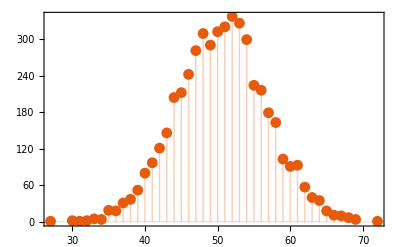

```mathematica
Tally[Map[tukey, Permutations[Range[1,9]]]]
ListPlot[SortBy[Tally[Table[tukey[RandomSample[Range[1,100]]], {i, 1, 5000}]], First], Filling -> Axis, PlotTheme -> { "Scientific"}]
```

This would be a great way to find the pivot element for the famous quicksort algorithm. Speaking of which, since all the hard work of the quicksort algorithm is done in the pivot selection, the rest of this famous algorithm is just a couple of lines of recursive code. (For simplicity, the following implementation assumes that all elements are distinct, which guarantees that the pivot element will produce at least one element on both sides of the recursion, which guarantees that the recursion will not get stuck in on place forever.) With the near virtual guarantee of always getting a good pivot element that is at least reasonably close to the true median, the potential collapse into quadratic running time does not emerge, as we can see by plotting the running times of this algorithm for randomly permuted lists between one thousand and twenty thousand elements.

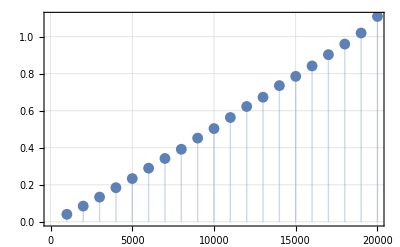

```mathematica
quicksort[{x_}] := {x};
quicksort[{x_,y_}]:= {x, y} /; x ≤ y;
quicksort[{x_,y_}] := {y, x};
quicksort[items_ /; Length[items] > 2]:= With[{pivot = tukey[items]},
Join[quicksort[Select[items, (# ≤ pivot)&]], quicksort[Select[items, (# > pivot)&]]]];

ListPlot[Table[{n,First[Timing[quicksort[ RandomSample[Range[1,n]]]]]},{n,1000,20000,1000}], Filling -> Axis, PlotTheme -> "Detailed"]
```

An important Mathematica idiom that could be called "lazy assignment of eager assignments" allows us to easily memoize the results of recursive functions so that whenever the same arguments are encountered in the future calls of that function, the result is looked up from Mathematica's definition knowledge base instead of evaluated again all the way down from scratch. Without memoization, computing Fibonacci numbers with straightforward recursion would take exponential time with respect to n, since the result would effectively get accumulated by adding one to it each time. (Note also the correct spelling of “memoize” when used in this technical sense, so that there is no letter r anywhere in this word.)

```mathematica
fib[n_/;n>2] := fib[n] = fib[n-1] + fib[n-2];
fib[2] = 1;
fib[1] = 1;
fib[101]
```

573147844013817084101

(The next one is just to make sure. After all, we are known to make mistakes.)

```mathematica
Fibonacci[101]
```

573147844013817084101

Memoization is an example of the more fundamental phenomenon of time-space tradeoff that is encountered all over computer science and programming. We can either make some program faster by having it cache the repeated intermediate results in memory, or we can make that program use less memory by having it compute the same results many times, but not both. The fundamental difference between space and time is that space can be reused later, whereas time that is spent is gone forever. Since computer memory in both RAM and disk space keeps getting cheaper at a much faster rate than the processor speed that we never seem to have enough of, we are usually happy to be able to use more RAM to shave down the computation time. All programming is merely an exercise in caching, and good caching will soon lead to cha-ching.

The subset sum problem encountered in the earlier lesson can be solved using patterns and recursion. The base cases of this recursion are the observations that any list has a subset whose sum is zero (just take the empty subset), whereas the empty list has no subsets that would add up to any nonzero goal. Otherwise, you either take the first element of the list into this subset, in which case the remaining goal equals the previous goal minus that first element; or you don’t take in the first element, in which case the goal remains the same. Examine both ways recursively, and if either way finds a solution, the answer is True. The symbol || (or alternatively ∨) is used to combine two truth values with logical or, evaluating to True if either or both of its operands evaluate to True. (This logical or should be distinguished from the “or” of natural language where the answer to the question “Would you like coffee or tea?” can’t be just “Yes”, unless you are talking to Sheldon Cooper. The “or” of the natural language is much closer to the exclusive or of Boolean algebra.)

```mathematica
subsetsum[li_, 0] := True;
subsetsum[{}, goal_] := False;
subsetsum[li_, goal_] := subsetsum[Rest[li],goal -First[li]] || subsetsum[Rest[li], goal];
subsetsum[{5, 8, 12, 13, 16, 21, 33}, 64]
```

False

The running time of this function is still inherently exponential in the worst case, but its memory use is only linear. We could use memoization to optimize the calculation of repeated subproblems to speed up the search for large problems, with the cost of exponential memory use.

Coin changing is another classic recursion exercise gives a list of different coin denominations, all of which are assumed to be available in unlimited quantities inside the checkout till. The problem then asks to compute how many different ways the given amount of money could be split into coin change using these coin denominations. Regardless of what coins you have, there is exactly one way to give back the zero amount, and regardless of the amount, there is no way to give it if there are no coins available. Otherwise, either you take in one coin of the largest remaining denomination, or you don’t. Since these possibilities are mutually exclusive, we can recursively compute the number of both ways and then simply add up the results of both calls. Since these calls lead to disjoint solutions, there is no issue of subtracting the overlap from the answer, unlike in combinatorial problems in general.

```mathematica
coincount[0, _] = 1;
coincount[n_, {}] = 0;
coincount[n_, coins_] := coincount[n, coins] = If[n ≥ Last[coins], coincount[n - Last[coins], coins] + coincount[n, Most[coins]], coincount[n, Most[coins]]] ;
coincount[99, {1, 2, 7, 11, 24, 55}]
```

2596

An alternative syntax for conditions uses a question mark followed by that condition given as a function. Such a pattern matches the expressions for which that function evaluates to True.

```mathematica
{1, 2, 3, 4, 5, 6} /. x_?EvenQ -> "hello"
```

{1,hello,3,hello,5,hello}

Next, we use lists and pattern matching rules to solve a problem that is otherwise quite difficult to solve using traditional eagerly evaluated imperative programming languages, but becomes a breeze with the symbolic computation of Mathematica.  The problem gives you a list of integers, and your task is to place mathematical operations between them, possibly using parenteheses, so that the resulting expression equals the given goal value. Since Mathematica already treats everything as a symbolic expression, representing integers fraction expressions would not be problematic, except that while building up an expression, we need a way to temporarily disable the Mathematica pattern matching so that the expression 1 / (2 + 3) remains exactly that instead of becoming 1 / 5. Fortunately, the function Hold that can be applied to any expressions tells Mathematica not to touch that expression. To evaluate the expression, ReleaseHold cancels the effect of Hold ands lets the evaluation proceed normally.

The function combine generates a list of all possible ways to combine the given left and right subexpressions under the four basic arithmetic operations. We also define another function evaluate to evaluate the given expression recursively, removing all the Hold heads from the expression to allow the evaluation to proceed all the way down. This is needed to ensure that these expressions can be combined by division only if the right expression does not evaluate to zero.

```mathematica
evaluate[HoldForm[op_[l_,r_]]] := op[evaluate[l],evaluate[r]];
evaluate[x_] := x;
combine[l_,r_/;evaluate[r] ≠ 0]:= {HoldForm[Plus[l,r]], HoldForm[Subtract[l,r]], HoldForm[Times[l,r]],HoldForm[Divide[l,r]] };
combine[l_,r_] := {HoldForm[Plus[l,r]], HoldForm[Subtract[l,r]], HoldForm[Times[l,r]]};
combine[2,3]
```

{2+3,2-3,2 3,2/3}

The function split goes through all the possible ways to choose the splitting position in the given list to separate the elements that become the left subexpression and the right subexpression.

```mathematica
split[items_] := Table[{items[[1;;i]], items[[i+1;;Length[items]]]},{i,1,Length[items]-1}];
split[{1,2,3,4,5}]
```

{{{1},{2,3,4,5}},{{1,2},{3,4,5}},{{1,2,3},{4,5}},{{1,2,3,4},{5}}}

The two previous functions defined and working, all possible ways to combine the given values into expressions can now be generated with a recursive pattern. There is an exponential number of ways to generate not only the possible tree shapes but to choose one of the four arithmetic operators into their nodes, as evidenced by the list of possible expressions that you can generate from leaf nodes that carry the values 1, 2, 3 in this order.

```mathematica
expressions[{x_}] := {x};
expressions[items_]:=Flatten[Table[Flatten[Table[combine[l,r],{l,expressions[sp[[1]]]},{r,expressions[sp[[2]]]}],2],{sp, split[items]}]];

exps = expressions[{1,2,3}];
values =Map[evaluate, exps];
Thread[(#1->#2)&[exps, values]]
```

{1+(2+3)→6,1-(2+3)→-4,1 (2+3)→5,1/(2+3)→1/5,1+(2-3)→0,1-(2-3)→2,1 (2-3)→-1,1/(2-3)→-1,1+2 3→7,1-2 3→-5,1 (2 3)→6,1/(2 3)→1/6,1+2/3→5/3,1-2/3→1/3,1 2/3→2/3,1/(2/3)→3/2,(1+2)+3→6,(1+2)-3→0,(1+2) 3→9,(1+2)/3→1,(1-2)+3→2,(1-2)-3→-4,(1-2) 3→-3,(1-2)/3→-1/3,1 2+3→5,1 2-3→-1,(1 2) 3→6,(1 2)/3→2/3,1/2+3→7/2,1/2-3→-5/2,1/2 3→3/2,(1/2)/3→1/6}

Solving the problem that originally led us to this mess is now but the simple operation of selecting from the generated list of symbolic expressions precisely those that evaluate to the goal value. This function can be easily extended to solve the simple variations of this problem where the order of the elements can be permuted, or where you are allowed to use only some subset of these numbers. To try out these functions, we can find out how many ways the simple fraction of one fifth can be constructed by cleverly combining the integers from 2 to 5.

```mathematica
solveMaintainOrder[goal_, items_] := Select[expressions[items],(evaluate[#] == goal)&];
solveCanPermute[goal_, items_] := Flatten[Table[solveMaintainOrder[goal, pitems],{pitems, Permutations[items]}]];
solveSubsets[goal_, items_] := Flatten[Table[solveCanPermute[goal, is], {is, Subsets[items,{1,Length[items]}]}],2];

solveMaintainOrder[1/5, Range[2,5]]
solveCanPermute[1/5, Range[2,5]]
solveSubsets[1/5,Range[2,5]]
```

{(2+(3-4))/5,((2+3)-4)/5}

{(2+(3-4))/5,((2+3)-4)/5,(2-(4-3))/5,((2-4)+3)/5,3-(2+4/5),(3-2)-4/5,(3+(2-4))/5,((3+2)-4)/5,(3-(4-2))/5,(3-4/2)/5,((3-4)+2)/5,3-(4/5+2),(3-4/5)-2,(5-4)/(2+3),(5-4)/(3+2)}

{(3-2)/5,(4-3)/5,(2+(3-4))/5,((2+3)-4)/5,(2-(4-3))/5,((2-4)+3)/5,3-(2+4/5),(3-2)-4/5,(3+(2-4))/5,((3+2)-4)/5,(3-(4-2))/5,(3-4/2)/5,((3-4)+2)/5,3-(4/5+2),(3-4/5)-2,(5-4)/(2+3),(5-4)/(3+2)}

As our next interesting problem, we use memoization to recursively compute the number of possible bidding sequences in the card game of bridge. Each bid consists of level between one and seven, inclusive, and strain, which is either one of the four suits or notrump. The bidding for four players who play as pairs of North-South against East-West rotates clockwise so that when it is his turn to bid, the player can either pass, or make some contract bid that is higher than the current highest active contract bid in that either its level is strictly higher than that of the current highest bid, or it has the same level but uses a higher strain when ranked in the order of clubs < diamonds < hearts < spades < notrump. Also, if the current highest bid was made by one of the opponents, a player can double it, and after a double by an opponent, a player can redouble. (There exists no re-redouble in bridge.) The bidding ends when three passes are made consecutively, or when the hand is passed out after four initial passes when nobody felt like they had an opening hand.

First, we define an auxiliary function higherbids that generates a list of higher contract bids than the one it gets as parameter. The strains are numbered from 1 to 5, and the levels are numbered from 1 to 7.

```mathematica
higherbids[8, strain_] := {};
higherbids[level_, strain_] := Join[
Table[{level, s}, {s, Range[strain+1, 5]}], 
Flatten[Table[{l, s}, {l, Range[level+1, 7]}, {s, 1, 5}], 1]
];
```

The recursive function bridgeseq is given four parameters. First two are the level and strain of the current highest active contract bid. The third is the number of passes that have been made after the most recent non-passing bid that kept the bidding alive, and the fourth gives the information of whether the most recent non-passing bid was a double or a redouble. The function is memoized so that the repeated subproblems will not cause the evaluation to take exponential time. To compute the number of possible sequences that continue from the current state, we add up the sequences that start with each of the possible contract bids, and in the cases where double or redouble is possible, add the numbers of the sequences starting with doubling or redoubling to the result. Either way, passing is always possible, so we add all the sequences to the result.

```mathematica
bridgeseq[level_, strain_, 3, double_] := 1 /; level > 0
bridgeseq[0, strain_, 4, double_] := 1;
bridgeseq[level_, strain_, passes_, double_] :=
bridgeseq[level, strain, passes, double] =
Total[Table[bridgeseq[b[[1]], b[[2]], 0, 0], {b, higherbids[level, strain]}]]+ If[level > 0 &&double == 0 && (passes == 0 || passes == 2), bridgeseq[level, strain, 0, 1], 0] + If[level > 0 && double == 1 && (passes == 0 || passes == 2), bridgeseq[level, strain, 0, 2], 0] + bridgeseq[level, strain, passes + 1, double] ;

bridgeseq[0, 5, 0, 0]
```

128745650347030683120231926111609371363122697557

In addition to the total number, we can ask how many sequences can be generated from any starting point in bidding. For example, how many different ways are there continue when the current bid is three spades that the next opponent doubled?

```mathematica
bridgeseq[3, 4, 0, 1]
```

46558346913302666917724553216

The vast majority of these possible bidding sequences are pretty much nonsensical (at least in the absense of both pairs using highly unconventional bidding systems) and could never be encountered in actual play. (For example, somebody opens 1NT, and then jumps to six clubs in response to his partner’s invitational 2NT, or that somebody passes his partner’s five hearts control showing cuebid after the opponents have already bid hearts... then again, never mind.) However, the readers interested in combinatorics can note the curious result that there exist far more different ways to bid a bridge deal than there are to actually deal out the hands!

```mathematica
N[% / (52! / (13!^4)), 5]
```

0.8679

Then again, someone with a knack for combinatorial thinking would have avoided all this work and used a shorter combinatorial formula. But this is the very advantage of programming, that it allows us to do our thinking in smaller chunks that the computer with then helpfully memoize for us. Sure, the explicit closed form formula is shorter and that way simpler, but let’s see a show of hands, how many readers would have come up with the following combinatorial formula all by themselves?

```mathematica
(22^35-1)/3 *4 + 1
```

128745650347030683120231926111609371363122697557

Our illustration of pattern matching continues with some string processing with Mathematica. As mentioned in the previous document, basically for every list function Foo there exists the corresponding function StringFoo that does the same operation for text strings. For example, StringLength, StringTake, StringDrop, StringJoin, StringCases, StringPosition, et cetera. For string matching, StringExpression, or its more common infix form ~~, can be used to create string patterns. These patterns can then be given as arguments to functions that operate on strings. Inside a StringExpression, a single underscore matches one character, double underscore matches one or more characters, and triple underscore matches zero or more. For functions that look for multiple matches, the option Overlap can be used to allow matches that partially overlap.

```mathematica
StringCases["aababaabbaabb", "b" ~~ __ ~~"bb"]
StringCases["aababaabbaabb", "b" ~~ __ ~~"bb", Overlaps -> True]
```

{babaabbaabb}

{babaabbaabb,baabbaabb,bbaabb,baabb}

Useful built-in character classes such as WordCharacter, LetterCharacter, DigitCharacter and WhitespaceChraracter and be used to match those kinds of characters. The function StringSplit works similarly to StringCases in that it produces a list of substrings, but in StringSplit, you specify the separators instead of the words that you are looking for. The postfix operators .. and ... require the pattern to be repeated one or more times, or zero or more times. Note that it is possible for some extracted substring to be empty, which happens when one separator string is immediately followed by another separator string. The function Except can be used to negate a character class.

```mathematica
Map[Framed[#]&, StringSplit["One;Two;Three;Four", ";"]]
Map[Framed[#]&,StringSplit["Hello there, how are you?", WhitespaceCharacter..]]
Map[Framed[#]&,StringSplit["Hello there, how are you?", WhitespaceCharacter...]]
Map[Framed[#]&,StringSplit["Hello there, how are you?", Except[WhitespaceCharacter]]]
```

{One,Two,Three,Four}

{Hello,there,,how,are,you?}

{H,e,l,l,o,,t,h,e,r,e,,,,h,o,w,,a,r,e,,y,o,u,?}

{ ,,,,,, ,,, ,,, }

The functions ToString and ToExpression can be used to perform conversions between strings and expressions both ways. Various options can be used to control the behaviour of the conversion depending on what form you want the result to be in.

```mathematica
exp = x^Sqrt[♣] + y^☺;
exps = ToString[exp, InputForm];
exp2 = ToExpression[exps, StandardForm];
exps // FullForm
exp2 // FullForm
```

"x^Sqrt[\[ClubSuit]] + y^\[HappySmiley]"

Plus[Power[x,Power[\[ClubSuit],Rational[1,2]]],Power[y,\[HappySmiley]]]

In addition to simple matching with StringExpression, Mathematica offers regular expressions and their matching with the function RegularExpression. Its power of computation is almost to the level of the Perl programming language, but not quite, since as they say, “Only Perl can parse Perl”. However, for the enthusiasts of regular expressions as a powerful tool to saw through complex problems, Mathematica has everything they could possibly want in that field. The syntax of the regular expressions and the special character classes is exactly the same as it is in every other programming environment.

As an exercise of rule-based programming for strings, the task is to write a function canbuild(s, pats, n) that determines if its first argument string s can be somehow constructed from the list of patterns pat given in the second argument, when patterns can be reused. The base cases of recursion are that an empty string can always be built from any set of patterns, and that a nonempty string can’t be built from an empty list of patterns. Otherwise, loop through the list of patterns looking for those that match the beginning of the string, and try to recursively build the rest of the string with the patterns.

```mathematica
canbuild[s_String, pats_List] := canbuild[s, pats, Length[pats]];

canbuild["", pats_, n_Integer] := True;
canbuild[s_String, pats_List, 0] := False; 

canbuild[s_String, pats_List, n_Integer] := 
(StringLength[s] ≥ StringLength[pats[[n]]] && StringTake[s, StringLength[pats[[n]]]] == pats[[n]] &&canbuild[StringDrop[s, StringLength[pats[[n]]]], pats, Length[pats]]) || canbuild[s, pats, n-1];
```

To try out this function, we shall create a list of random patterns (removing the duplicate elements) and then another list of random longer strings, and see which of the latter can be built from these patterns. To make at least some solutions exist with a good probability, we use only the letters from a to e, which happen to reside in the character codes from 97 to 101.

```mathematica
pats = Table[FromCharacterCode[RandomChoice[Range[97, 101], RandomInteger[{2,3}]]], {40}];
pats =Sort[DeleteDuplicates[pats]]
ss = Table[FromCharacterCode[RandomChoice[Range[97, 101], RandomInteger[{6,8}]]], {30}];
ss = Sort[DeleteDuplicates[ss]]
Select[ss, (canbuild[#, pats])&]
```

{aa,ab,ac,adc,add,ae,aee,ba,bae,bb,bc,bcb,bd,bdd,be,ca,cba,cbd,cc,ccb,ccc,ce,cee,dac,db,dc,de,dea,ea,eaa,ebd,ebe,ec}

{aaaeeebe,abcdaaca,acbacabd,acbdab,acedda,aecadbba,badabbae,badbecdb,badecc,bbdabad,bbdedcd,bcbbcecc,bcccabd,bcdcbabe,bcecbbd,bcedca,beeeee,cbdeadd,ccccbaae,cebaabae,cebdbcc,cedddead,dabeac,dabebda,dcacbc,dcccade,dcdbaae,deddbdc,ebbeecd,ebcceeca}

{aaaeeebe,acbacabd,acbdab,aecadbba,badbecdb,badecc,bcbbcecc,bcdcbabe,ccccbaae,cebaabae,dcacbc}

## Additional examples of rule functions

The pattern definitions that you make for a symbol are said to be the downvalues of that symbol. When you provide additional rules for your symbol when they are passed as arguments to other symbols, you are providing upvalues for those symbols. The built-in symbols and functions are protected against accidental manipulation, but you can Unprotect them as long as you know what you are doing. (Using suitably chosen tactical patterns to redefine and extend the built-in functions of Mathematica could seriously mess up the functionality of the entire system and make it unpredictable.)

```mathematica
Unprotect[Plus];
Plus[lenny, 0] = lenny;
Plus[lenny, k_/; k>0] = Plus[carl, k-1];
Plus[carl, 0] = carl;
Plus[carl, k_/; k>0] = Plus[lenny, k-1];
Protect[Plus];
lenny + 17
8 +carl
```

carl

carl

The ability to define rules and patters allows you to write entire axiom systems that encompass the known fundamental truths about some formal system, from which other truths can then be logically inferred with pattern matching and rules without knowing or caring what those symbols and names mean, or which particular entity of the problem domain we assign them to refer to. Note also that Mathematica already knows that the function Plus is symmetric, so its pattern matching correctly found the result for the expression 8 + carl. Were the function Plus not symmetric, the inference engine could not simplify this expression any further.

As a cute little sidebar, conditional patterns come handy in defining and solving delay differential equations where the differentials at time t depend not just on the current state, but on the values of in earlier times. Suitably chosen equations can make the state of the system evolve in chaotic and unpredictable ways that has no hope of being expressible with analytical functions, and must therefore necessarily be examined numerically.

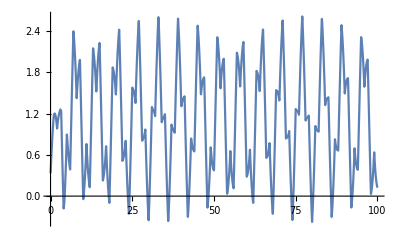

```mathematica
ddsol = NDSolve[{y'[t] == Cos[t] -2y'[t-1]/(t+5) + Sign[y'[t-2]], y[t/; t≤ 0] == 1/3}, y, {t, 0, 100}];
Plot[y[t]/. ddsol, {t, 0, 100},PlotRange -> All]
```

Parametrically plotting the difference between the states y[t] and y[t-1] also produces an interesting function.

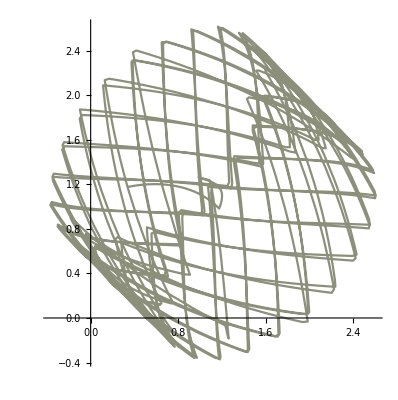

```mathematica
ParametricPlot[{y[t-1], y[t]} /. ddsol, {t, 1, 100}, ColorFunction -> "Rainbow", PlotRange->All]
```

About a decade ago, the Fizzbuzz problem generated much interest online in the programmer forums because of the amazing claim made by one professional job interviewer. He had observed that most computer science graduates simply can’t program at all, not even the simplest problems that should be lab exercises after the first couple of weeks of the first programming course. Fizzbuzz is an example of such a Mickey Mouse problem that any second year computer science student should be able to solve in his sleep n theory. In practicse, this silly problem causes insurmountable problems for many applicants for entry level programmer job who look good on paper and are supposed to have a bachelor’s degree in computer science from a reputable university, yet do no better than the graduates of any diploma mill that grants degrees based on “life experience”.

In the original children’s party game that inspired this problem, the task is to say the numbers of the given range in order but so that whenever a number is divisible by 3, say “fizz”; when the number is divisible by 5, say “buzz”; and when it is divisible by both 3 and 5, say “fizzbuzz”. In all other cases, you just say the number itself. There are many little pitfalls in this problem to get its implementation working, most importantly writing the steps of the if-else ladder in correct order.

```mathematica
fizzbuzz[x_] := x;
fizzbuzz[x_/; Mod[x, 15] == 0] := "fizzbuzz";
fizzbuzz[x_ /; Mod[x, 5] == 0] := "fizz";
fizzbuzz[x_ /; Mod[x, 3] == 0] := "buzz";
Map[fizzbuzz, Range[1, 100]]
```

{1,2,buzz,4,fizz,buzz,7,8,buzz,fizz,11,buzz,13,14,fizzbuzz,16,17,buzz,19,fizz,buzz,22,23,buzz,fizz,26,buzz,28,29,fizzbuzz,31,32,buzz,34,fizz,buzz,37,38,buzz,fizz,41,buzz,43,44,fizzbuzz,46,47,buzz,49,fizz,buzz,52,53,buzz,fizz,56,buzz,58,59,fizzbuzz,61,62,buzz,64,fizz,buzz,67,68,buzz,fizz,71,buzz,73,74,fizzbuzz,76,77,buzz,79,fizz,buzz,82,83,buzz,fizz,86,buzz,88,89,fizzbuzz,91,92,buzz,94,fizz,buzz,97,98,buzz,fizz}

The sharp-eyed reader surely noticed that several of these rules would match some values of x. For example, if x equals 15, all four rules for fizzbuzz would match it! So how does Mathematica determine which rule to use? In a situation like this, the order in which the rule definitions were originally given determines which one of these matching rules gets applied, same as the if-else ladders work in imperative programming languages. Only one rule is applied in pattern matching, unlike in the Prolog programming language where all the rules that match are used one at the time until you explicitly force the matching the end with the cut operator. However, Mathematica will rearrange the rules whenever one is clearly more specific than the other one. Therefore there is no harm to place the “none of the above” rule in the first position in the above list.

The single underscore always matches one expression. (For matching sequences of expressions, the double underscore matches any sequence of one or more expressions, and the triple underscore matches zero or more expressions.) This allows us to write what are essentially recursive Prolog functions, just with a slightly different syntax. As an example of this sort of programming, we next write a function everyother that, when applied to a list, produces a list that contains the elements in the odd-numbered positions of that list. We can do this by writing the rules for the base cases (for this particular problem, the lists that contain either zero or one elements), and then a rule for the general case of two elements followed by a sequence of zero or more elements.

```mathematica
everyother[{}] := {};
everyother[{x_}] := {x};
everyother[{x_, y_, rest___}] := Prepend[everyother[List[rest]], x];
everyother[{1,2,3, 4, 5, 6, 7, 8}]
```

{1,3,5,7}

As usual, if the argument doesn’t match any of the rules provided for your function, Mathematica leaves the expression as it is.

```mathematica
everyother["hello world"]
```

everyother[hello world]

Every Prolog textbook begins with examples of this nature, at least after the first chapter of compulsory examples of familial relationships and the logical formulas that govern them. Once you understand these techniques in Mathematica, you would only need to learn the Prolog syntax to be able to write logic programs in Prolog and be a part of that elite cadre. But why would you bother, since you can do all this stuff in Mathematica with much flashier results?

```mathematica
patsum[{}] = 0;
patsum[{x_, rest___}] := x + patsum[List[rest]];
patsum[Range[1, 100]]
```

5050

```mathematica
removedup[{}] = {};
removedup[{x_}]:= {x};
removedup[{x_, y_, rest___} /; x== y] := removedup[Prepend[List[rest], y]];
removedup[{x_, y_, rest___} /; x≠ y] := Prepend[removedup[Prepend[List[rest], y]], x];
removedup[{1, 1, 1, 2, 2, 3, 3, 3, 3, 3, 4, 5, 5, 5,6}]
```

{1,2,3,4,5,6}

```mathematica
range[start_, end_] := {} /; start > end;
range[start_, start_] := { start };
range[start_, end_] := Prepend[range[start+1, end], start];
range[4, 10]
```

{4,5,6,7,8,9,10}

```mathematica
subsetQ[list_, {}] = True;
subsetQ[{}, list_] = False;
subsetQ[list_, {x_, rest___}] := MemberQ[list, x] && subsetQ[list, List[rest]];
subsetQ[Range[1, 10000, 2], Table[Prime[i], {i, 2, 100}]]
```

True

Now that we started on this path, the next example to include by law is the old chestnut of Tower of Hanoi, a problem that is  older than radio. In the following set of pattern matching rules, note how there is no law of nature or man saying that you can’t define the same function to operate on different numbers of arguments. People steeped in the thinking of the object-oriented paradigm would say that the function hanoi has been overloaded. (Like many other words in computer science such as “lazy” or “fair”, this word is not a pejorative or indicative of any kind of an error, but simply an acknowledgement of the state of affairs that is neither good or bad by itself.) The following solution produces the list of moves that to solve the problem for n disks. (Many other solutions are possible, but this recursion is surely the most straightforward solution.)

```mathematica
hanoi[n_] := hanoi[n, 1, 2, 3];
hanoi[1, src_, mid_,tgt_] := { src -> tgt};
hanoi[n_ /; n > 1, src_, mid_, tgt_] :=
Join[
hanoi [n-1, src, tgt, mid],
hanoi[1,src, mid, tgt],
hanoi[n-1, mid, src, tgt]
];
hanoi[3]
```

{1→3,1→2,3→2,1→3,2→1,2→3,1→3}

What would happen if we built up a random expression from the given set of possible pieces, and then tried to evaluate this expression? The function rexp[n] creates a random expression of depth n, with numerical constants and the two symbols x and y serving as possible leaf nodes, and a couple of functions that operate in the range [-1, 1] serve as the heads of the expressions that are recursively defined from level n - 1. For each non-leaf node, we flip a coin whether to make that function unary or binary.

```mathematica
unary = {Sin[π#]&, Cos[π#]&, (2*LogisticSigmoid[#]-1)& };
binary = {(#1*#2)&,((#1+#2)/2)&, (Max[{#1, #2}])&};
rexp[0] := RandomChoice[{x, y, RandomReal[{-1, 1}]}];
rexp[x_/; x> 0] := If[
RandomInteger[2] == 1,
With[{h = RandomChoice[unary]}, h[rexp[x-1]]],
With[{h = RandomChoice[binary]}, h[rexp[x-1], rexp[x-1]]
]];

Grid[Partition[Table[rexp[3], {i, 1, 12}], 3], Frame->All]
```

Max[Cos[2.59534 x],Sin[π Max[x,y]]] | 1/2 (0.82765+1/2 (1/2 (0.0653269+y)+Max[-0.00457094,x])) | Cos[π Cos[3.01209 y]]
-1+2 LogisticSigmoid[Sin[π (-1+2 LogisticSigmoid[y])]] | -1+2 LogisticSigmoid[Max[0.26449,-0.85483 y,y]] | Max[1/2 x^2 (0.695634+y),Cos[π y] Sin[π y]]
-1+2 LogisticSigmoid[0.356283 Sin[π x]] | 1/2 (1/2 (x y+Cos[π x])+Max[y,(x+y)/2]) | Sin[1/2 π (-0.200979+x)] Sin[π Cos[π x]]
Max[1/2 (x y+Max[x,y]),1/2 (0.629118 y+Sin[π x])] | Max[0.472695 y,Cos[π x],Cos[π y],Sin[π x]] | 1/2 (-1.99431+2 LogisticSigmoid[x]) Max[-0.0535989 x,x y]

Let’s plot a grid of random expressions to see a “gallery” of random abstract art. While we are at it, we might as well also choose the colour functions randomly. We need to use With to define the formula used for each pixel of the table, because otherwise, the formula would be generated randomly again for each pixel, producing only random noise. We leave it as exercise for the reader to find more unary and binary functions that produce interesting and aesthetical random patterns.

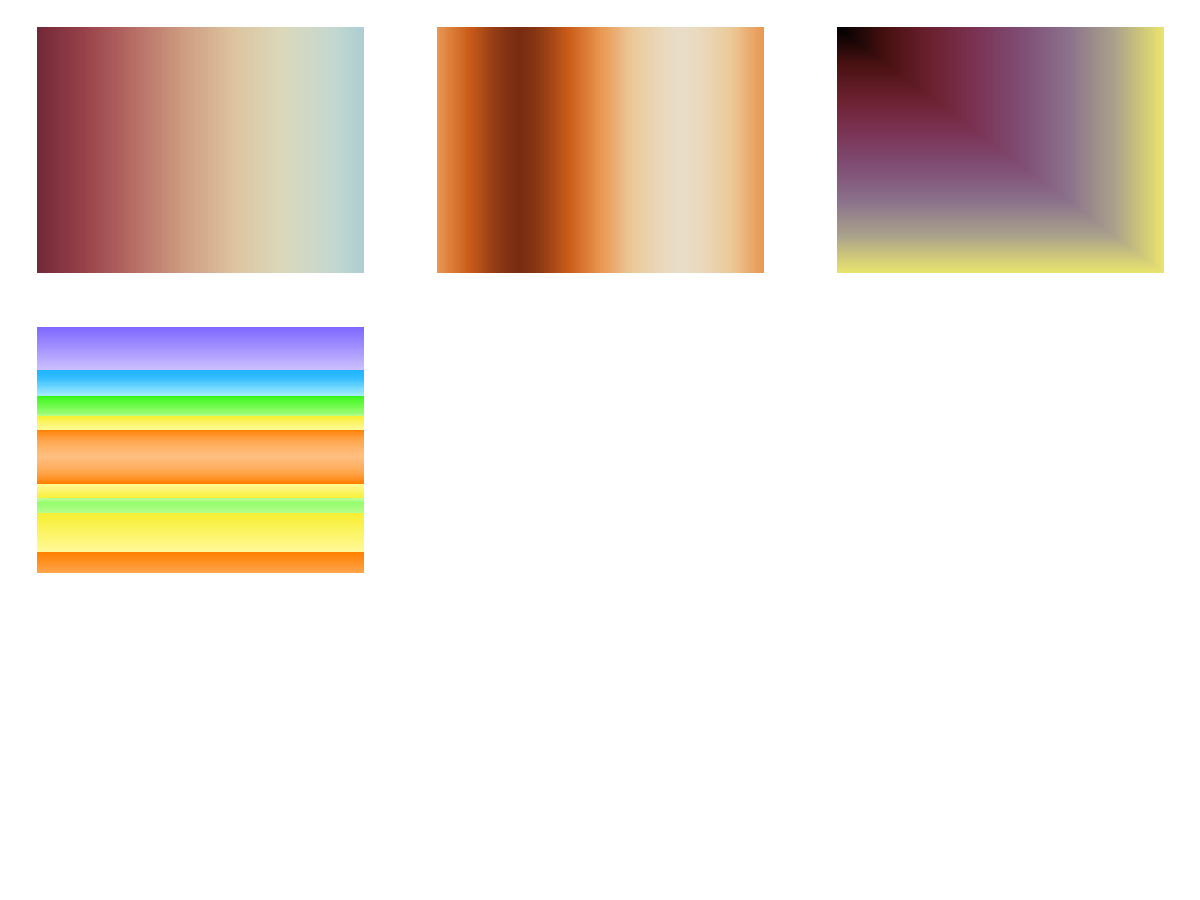

```mathematica
Grid[Partition[Table[With[{formula = rexp[1 + Floor[i/2]]},MatrixPlot[Table[formula, {x, -1, 1, .01}, {y, -1, 1, .01}], ColorFunction -> RandomChoice[ColorData["Gradients"]],Frame-> False, Axes->False, ImageSize -> {200, 200}]], {i, 1, 9}], 3]]
```

In most textbooks, recursion is usually explained with adding integers and other boring things. Using Mathematica’s built-in image processing primitives inside our recursively defined rules allows us to construct interesting shapes with image composition analogous to the way that we used addition on integers. Integers are beautiful in their own way, but so are images, in a different way.

```mathematica
nestimg[img_, d_Integer] :=  Module[{smaller}, If[d == 0, img,
smaller = nestimg[img, d-1] ;
smaller = ImageResize[smaller, ImageDimensions[smaller][[1]] / 2];
smaller = ImageAssemble[{{smaller}, {smaller}}];
ImageAssemble[{img, smaller}]
]
];
lena = ImageCrop[ImageResize[ExampleData[{"TestImage","Lena"}], 300], {250, 300}];
nestimg [lena, 6]
```

-Graphics-

```mathematica
checker[img_, d_Integer] :=Module[{smaller}, If[d == 0, ImageResize[img, {Max[ImageDimensions[img]], Max[ImageDimensions[img]]}],
smaller = checker[img, d - 1];
smaller = ImageResize[smaller, ImageDimensions[smaller][[1]] / 2];
ImageAssemble[{{smaller,ImageRotate[smaller, 3π/2]}, {ImageRotate[smaller], ImageRotate[smaller, π ] }}]
]
];
checker[lena, 3]
```

-Graphics-

The next spiral is more complicated since we must ensure that all assembled pieces match together perfectly. If we were allowed to assume that the width and height of the image are powers of two, the next function would be a lot shorter. Alas, we are not, so when we divide a piece in two so that the width of that piece is odd, the width of one of the resulting halves must be rounded up whereas the width of the other must be rounded down so that both widths are integers that add up exactly to the original width, leaving no ugly seams in the image. However, this illustrates an important principle of software engineering that the simplicity of use often necessitates the complexity of implementation. When dealing with a complex problem, that complexity has to end up somewhere. It is far better for the designer of some function to go through the effort of solving the problem as generally as possible once and for all, than it is to go for the simplicity of implementation and thus force each user of this function to solve the same problem again. (The same principle also explains why we have high-level programming languages in the first place.)

```mathematica
spiralimg[img_, 0] := img;
spiralimg[img_, d_ /; d>0] := Module[{w, h,nw, ne, north,sw, se, west, center},
{w,h} = ImageDimensions[img];
nw = ImageResize[ImageRotate[img, -π/2], {Floor[w/2], Floor[h/2]}];
ne = ImageResize[ImageRotate[img, -π/2], {Ceiling[w/2], Floor[h/2]}];
north = ImageAssemble[{nw, ne}];
se = ImageResize[ImageRotate[img, -π], {Floor[w/2], Ceiling[h/2]}];
sw = ImageAssemble[{ImageResize[ImageRotate[img], {Floor[Ceiling[w/2]/2], Floor[Ceiling[h/2]/2]}], ImageResize[ImageRotate[img], {Ceiling[Ceiling[w/2]/2], Floor[Ceiling[h/2]/2]}]}];
west = ImageResize[img, {Floor[Ceiling[w/2]/2], Ceiling[Ceiling[h/2]/2]}];
center = ImageResize[spiralimg[img, d-1], {Ceiling[Ceiling[w/2]/2], Ceiling[Ceiling[h/2]/2]}];
ImageAssemble[{{north},{ImageAssemble[{ImageAssemble[{{ImageAssemble[{west, center}]},{sw}}], se}]}}]
];

spiralimg[lena, 3]
```

-Graphics-

From the womanly graces of lovely Lena, we move on to the flags of the nations of the world as another source of colourful test images. However, for the function ImageAssemble to work correctly, we have to filter out three flags whose images have a wrong number of colour channels.

```mathematica
flags = Map[ImageResize[CountryData[#, "Flag"], {200, 200}]&, CountryData[]];
flags = Select[flags, (ImageChannels[#] == 4)&];
```

Let’s try to use the earlier nestimg function so that each part is a randomly chosen flag.

```mathematica
randomflag := RandomChoice[flags];
Grid[Table[nestimg[randomflag, 5], {i, 1, 3}, {j, 1, 3}]]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

Close but no cigar. Even though we used the lazy assignment := to define the quantity randomflag, it still gets evaluated only once when Mathematica starts simplifying the nestimg expression, so each nested image ends up using one and the same flag throughout. Of course, any language must allow the programmer to somehow make the distinction between “Choose a random flag and perform the operation on it many times” and “Perform the operation many times, choosing a random flag each time”, since both of these must be algorithmically possible! One way to do the latter is to rewrite the function to maintain the flag on Hold, and then release the hold in the places where the image has to be explicit.

```mathematica
nestimglazy[img_, d_Integer] :=  Module[{smaller1, smaller2, smaller}, If[d == 0, ReleaseHold[img],
smaller1 = nestimglazy[img, d-1] ;
smaller1 = ImageResize[smaller1, ImageDimensions[smaller1][[1]] / 2];
smaller2 = nestimglazy[img, d-1] ;
smaller2 = ImageResize[smaller2, ImageDimensions[smaller2][[1]] / 2];
smaller = ImageAssemble[{{smaller1}, {smaller2}}];
ImageAssemble[{ReleaseHold[img], smaller}]
]
];
Grid[Table[nestimglazy[Hold[randomflag], 5], {i, 1, 3}, {j, 1, 3}]]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

## Three major programming paradigms

Mathematica supports all of the three major programming paradigms of functional programming, rule-based programming, and the old school imperative programming. All of these styles can be freely mixed and matched depending on what is most convenient for the present needs, in the spirit of the realization that all programming is one to beging with anyway. However, as a general rule for programming in Mathematica, the traditional style imperative programming should nearly always be the last resort, used only when the more natural and powerful functional and rule-based approaches of Mathematica somehow fail to give you what you need. Most people who come from imperative programming backgrounds try to force Mathematica to do everything in the imperative paradigm, but in general “trying to write Fortran in any language” is the wrong approach for most problems.

Back in the dusty times of swords and sandals, it was perfectly possible for someone to be a perfectly good citizen, even a king, without being able to read or write or count past your fingers, toes and nose. Today we are surrounded by such a fire hose of all sorts of useful written material that those few of us who can’t read fall from the start so immensely behind the pack that they are simply irrelevant.

In our tumultuous times of chaotic and exponential processes, lopsided distributions and the average being over, computer science and programming, the street level praxis of logic and abstract thinking, are quietly approaching a similar fundamental shift in importance. During the horn-rimmed fifties, the ability to program the good room-sized kilobyte clunker by rerouting its wires and vacuum tubes allowed you to churn out boring tables of projectile ballistics. Today, the ability to program computers gives you an entry to a comfortable middle class indoor job out of the rain and pays your mortgage. In fifty years, even with the most pessimistic possible estimates of future computing power advances and their associated network effects, the ability to program the computer networks that will by then be so ubiquitous that the very word computer will have vanished from our language would let you to wield the practical powers of a minor Olympian deity.

In this spirit, behold our next test image. To quote the great man, everyone needs computer programming, as it will be the way we speak to the servants.

```mathematica
mccarthy = ImageResize[Import["http://www.xach.com/img/doing-it-wrong.jpg"], 240]
```

-Graphics-

```mathematica
pieces = ImagePartition[mccarthy, 20]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

Rotate the pieces using functional programming.

```mathematica
functionalrotation = ImageAssemble[Map[(ImageRotate[#1])&, pieces, {2}]]
```

-Graphics-

Rotate those pieces using rule-based programming.

```mathematica
rulebasedrotation = ImageAssemble[Replace[pieces, piece_ :> ImageRotate[piece], {2} ]]
```

-Graphics-

Although, come to think of it, why restrict ourselves only to rotations?

```mathematica
effects = { {"Posterization", 4}, {"MotionBlur", 15}, {"OilPainting", 5}};
ImageAssemble[Replace[pieces, piece_ :> ImageEffect[piece, RandomChoice[effects]], {2} ]]
```

-Graphics-

In principle, all three paradigms are equally powerful in the sense of computational universality: whatever you can do with one of these styles, you could always somehow do with either one of the other two, it just might be less convenient. As an illustration of this, let us implement map using rule-based programming.

```mathematica
map[f_, {}] := {};
map[f_, {x_}] := {f[x]};
map[f_, {x_, rest__}] := Prepend[map[f, List[rest]], f[x]];
map[foo, {1, 2, 3}]
```

{42[1],42[2],42[3]}

Of course, Map is basically substitution restricted to operate on terms at level 1. (See what happens if you leave out the level restriction. The substitution rule will be applied only once, to the entire list!)

```mathematica
map2[f_, list_] := Replace[list, x_ -> f[x], 1];
map2[foo, {1, 2, 3}]
```

{42[1],42[2],42[3]}

## Imperative programming with loops

In this much-ballyhooed imperative programming that for some reason about 99% of all actual code in the world is still written in, repetition and conditional statements are iterated to modify your data one small part at the time with some action. This builds up the desired result gradually from the initial values whose repeated modification leads to the end result. For doing repetition with loops, there are several functions to express the range of values you want to iterate over. In principle, all of these loops are equally powerful in that in principle, they can express the same computations. However, it is good to know all these loops, since they might feel more natural in different situations.

The simplest repetition construct in Mathematica is Do. (Those familiar with C, Java or similar programming languages should not be confuse this function with the similar-looking do-while construct of those languages.) You specify the range of values that you want to iterate over, and the action that you wish to take for each value in this range, very much like you defined a Table. Usually this action is some kind of assignment where you replace the old value of some variable with the new value. This is generally very similar to what the functions Range and Table do, and in fact, for most problems, the functional style would be the correct way to go.

Let us take the late John McCarthy to pieces once more, but now in the imperative style... or in the words of the great man himself, in the way a Chinese cook divides up a duck.

```mathematica
pieces2 = ConstantArray[0, Dimensions[pieces]];
Do [
pieces2[[i]][[j]] = ImageRotate[pieces[[i]][[j]]],
{i, 1, Length[pieces2]}, {j, 1, Length[pieces2[[i]]]}
];
imperativerotation = ImageAssemble[pieces2]
```

-Graphics-

Inside the loop, your loop counter variable always contains the current value whose turn it is to be iterated. An old naming convention in programming, dating back all the way to the fifties and the Fortran programming language, is to use the letters i, j, k for integer-valued loop counter variables, emulating the mathematical convention of using these letters as indices to vectors and matrices. For example, the sum of squares of the first ten positive integers would be calculated with the following loop.

```mathematica
result = 0;
Do[ result = result + i^2, {i, 1, 10}];
result
```

385

The most important downside of the imperative approach is its inherent inability to handle symbolic values that don’t evaluate to a concrete numerical result. Suppose we wanted to generalize the previous problem to compute the sum of squares of the first k integers, with k unknown at the time.

```mathematica
result = 0;
Do[ result = result + i^2, {i, 1, k}];
result
```

Do::iterb: Iterator {i, 1, k} does not have appropriate bounds.

0

Symbolic functions based on pattern matching of mathematical axioms have no problem handling such open-ended situations. This is the power of functional and ruled-based programming over the imperative paradigm: the latter can’t proceed until all the values that it needs are sufficiently well-defined.

```mathematica
Sum[i^2, {i, 1, k}]
With[{ϕ = GoldenRatio}, {Sum[(1/ϕ)^i,{i,1, Infinity}],Sum[(1/ϕ)^i,{i,1, Infinity,2}]}]
```

1/6 k (1+k) (1+2 k)

{2/(-1+√5),(1+√5)/(2 GoldenRatio)}

The function While is similar to Do, but instead of specifying the range of values with the beginning and end to iterate through, known at the time you first enter the loop, you specify a condition that determines how long to keep iterating. This is more convenient in problems where it might even be generally impossible to know beforehand how many rounds around the carousel you need to go until you capture that proverbial ring. For example, we can again generate the Collatz series from the given starting value.

```mathematica
result = {};
i = 17;
While[i > 1, AppendTo[ result, i]; If[Mod[i, 2] == 0, i = i / 2, i = 3i +1]];
result
```

{17,52,26,13,40,20,10,5,16,8,4,2}

Here is Euclid’s greatest common divisor algorithm implemented with While.

```mathematica
gcdwhile[a_, b_] := Module[{a2 = a, b2 = b},
If[a2 < b2, {a2, b2} = {b2, a2}];
While[b2 > 0, {a2, b2} = {b2, Mod[a2, b2]}];
a2
];
gcdwhile[75, 45]
```

15

Pattern matching rules could have solved this problem easier.

```mathematica
gcdpat[a_,0] := a;
gcdpat[0, a_] := a;
gcdpat[a_,b_] := gcdpat[b, Mod[a,b]];
gcdpat[75,45]
```

15

Note how all of these examples modify the values of the variables that represent the current state of the computation, erasing the old value when replacing it with the new value. This destructive assignment, otherwise completely unknown and even absurd in mathematics, is the very essence of imperative programming and imperative computation. Once again it bears repeating that in Mathematica, all these three major programming paradigms can be freely mixed whenever they are convenient.

For large lists, AppendTo can be a bit inefficient, since it has to create a separate copy of the list that has been built up so far every time that it appends a new element. As an alternative, Reap and Sow can be used to create lists one element at the time in situations where you don't need the entire list until its every element has been created. Every time that Sow is encountered, its current argument expression is pushed into a behind-the-scenes storage stack. Reap then collects these sown elements, however many there happened to be, producing a pair whose first element is the result of evaluating its expression argument, and the second element is a list of lists of elements that were sown by that expression. (Expressions could be sown using different tags, and Reap would then gather them to separate sublists.) An implementation of collatzlist where the elements are sown as they are iterated over:

```mathematica
collatzlist[n_] := Module[{dummy, result},{dummy, { result} } = Reap[i = n; While[i > 1, Sow[i]; If[Mod[i, 2] == 0, i = i / 2, i = 3i +1]]];
result
];
collatzlist[17]
```

{17,52,26,13,40,20,10,5,16,8,4,2}

User input and output are needed to implement most of the typical introduction to programming exercises such as the basic chestnut “Please enter your name.” [The user enters Bob.] “Hello there, Bob. How old are you?” [The user enters 42.] “You are an adult.” The functions in Mathematica for these operations are Input and Print. When writing long functions, indentation helps the reader to discern its nested structure. Fortunately, Mathematica can do the indentation automatically for you as you type in the code. All you have to do for your part is to press the return key to tell it where to start a new line. This is also a great bug-finding utility in that when the indentation stubbornly refuses to adjust the way it should, you know you have a missing or mismatched brace or argument somewhere. This example also contains the first comment in this entire tutorial, which are denoted in Mathematica between pairs of parentheses and asterisks. Usually we have no need for comments inside a Mathematica notebook, since the textual notebook cells such as the one you are reading right now contain all the commentary needed. One important task of comments in all languages is the ability to comment out some block of code so that it does not get executed but remains there for the human reader to easily bring back with a couple of keystrokes.

```mathematica
guessinggame[range_] := Module[ 
{secret = RandomInteger[{1, range}], guess = -1, tries = 0},
While[guess ≠ secret,
guess = Input["Guess the secret number:"];
tries++;
If[guess < secret, Print["Too small!"]];
If[guess > secret, Print["Too big!"]];
];
Print[StringJoin["You got it in ", ToString[tries], " guesses."]];
];
(* guessinggame[100] *)

(* previous statement intentionally commented out so that the notebook can be evaluated on its own without popping out dialogs *)
```

When evaluated, a function that consists of series of statements produces the evaluation of the last statement in its body.  Note that unlike other programming languages, no special return keyword is needed, since all your functions are still just symbolic expressions that are evaluated according to the internal rules of Mathematica. An expression composed as a chain of expression evaluates to the value of the last expression of the chain. Remember not to write a semicolon after that last expression just by the habit of your fingers, because if you do that, the returned expression is actually Null, the invisible statement that follows that semicolon inside the module body!

```mathematica
sumofpowers[x_, n_] := Module[
{i = 0},
result = 0;
While[i ≤ n, result = result + x^i; i++];
result
];
```

Let’s see if that worked.

```mathematica
sumofpowers[a+b, 5]
```

1+a+b+(a+b)^2+(a+b)^3+(a+b)^4+(a+b)^5

```mathematica
Sum[(a+b)^i, {i, 0, 5}]
```

1+a+b+(a+b)^2+(a+b)^3+(a+b)^4+(a+b)^5

Hunky dunky. However, because of deep and fundamental reasons in the theory of computability in computer science, logic and mathematics, any use of imperative structures in your functions pretty much makes your functions off-limits for Mathematica’s powerful mathematical reasoning engine.

```mathematica
Dt[sumofpowers[x, k], x]
```

0

```mathematica
Dt[Sum[x^i, {i, 0, k}]]
```

-((-1+x^(1+k)) Dt[x])/(-1+x)^2+(x^(1+k) (((1+k) Dt[x])/x+Dt[k] Log[x]))/(-1+x)

Fizzbuzz can also be an illustrative example for the proper application of imperative programming and loops. However, if the reader feels a slight twinge in his belly while comparing the next code to the rule-based solution above, that is really only a good thing. In the next example, the choice from three or more possibilities could always in principle be done by lexically nesting If functions, but using Which to list the possible alternatives one at the time is often more convenient and descriptive. This function operates in the spirit of pattern matching in that evaluates its conditions until it finds one that is True for which it then performs the associated action and skips the remaining conditions. (For those familiar with C, Java and related languages, Which is basically a turbocharged version of the switch statement in those languages in that the conditions can be arbitrarily complex instead of just hardcoded integer literals. And of course, the Mathematica function Which does not have the silly fallthrough behaviour that every programmer will never stop accidentally falling into.)

```mathematica
{dummy, {result}} = Reap[
Do[Which[
Mod[i, 15] == 0, Sow["fizzbuzz"],
Mod[i, 5] == 0, Sow["fizz"],
Mod[i, 3] == 0, Sow["buzz"],
True, Sow[i]
], {i, 1, 100}]];
result
```

{1,2,buzz,4,fizz,buzz,7,8,buzz,fizz,11,buzz,13,14,fizzbuzz,16,17,buzz,19,fizz,buzz,22,23,buzz,fizz,26,buzz,28,29,fizzbuzz,31,32,buzz,34,fizz,buzz,37,38,buzz,fizz,41,buzz,43,44,fizzbuzz,46,47,buzz,49,fizz,buzz,52,53,buzz,fizz,56,buzz,58,59,fizzbuzz,61,62,buzz,64,fizz,buzz,67,68,buzz,fizz,71,buzz,73,74,fizzbuzz,76,77,buzz,79,fizz,buzz,82,83,buzz,fizz,86,buzz,88,89,fizzbuzz,91,92,buzz,94,fizz,buzz,97,98,buzz,fizz}

## Solving problems with loops

As required by its constitution, every ten years the great nation of the United States of America holds a nationwide census to tally up the populations of its states. These counts will then determine the number of representatives that each state gets  out of the 435 that comprise the Congress. Since the number of seats assigned to each state can’t be fractional, this division is done according to the Huntington-Hill method. Each state is seeded with one seat to begin with, regardless of its population. The remaining seats are then distributed one at the time, each seat always going next to the state that has the highest priority quotient at the moment. The priority quantity of that state is updated to reflect its incremented number of seats, and the loop continues to the next round to deal out the next seat. The data that this function needs to operate is easy to acquire from Mathematica and Wolfram Alpha built-in geographical and sociological databases. Since the District of Columbia is not a state, we use Complement to remove it from the list of 51 entities given by Wolfram Alpha, even though we asked only for the fifty.

WolframAlphaQueryParseResults

EntityClass[AdministrativeDivision,AllUSStatesPlusDC]

```mathematica
usa = %;
```

```mathematica
fiftystates = Complement[EntityList[usa],{Entity["AdministrativeDivision", {"DistrictOfColumbia", "UnitedStates"}]}];
statenicks = EntityValue[ fiftystates, "Nicknames"];
populations = EntityValue[fiftystates, "Population"];
```

To keep the following function simple, we have to assume that there are never any ties between the priority quotients at any stage of this algoritm. This would be impossible anyway unless two states have the exact same population, since the square root operator will produce a different irrational number for every possible number of seats greater than 1, and therefore dividing two different integers is guaranteed to produce a different priority quotient regardless of the state populations and the current number of seats that they have received so far.

```mathematica
huntingtonhill[seats_, pops_] := Module[{pq, result, next, seatsremain},
result = Table[1, {i, 1, Length[pops]}];
pq = Map[(#/Sqrt[2])&, pops];
seatsremain = seats - Length[pops];
While[seatsremain > 0,
seatsremain--;
next = First[Position[pq, Max[pq]]];
result[[next]]++;
pq[[next]] = pops[[next]] / Sqrt[result[[next]] *(result[[next]]+1)];
];
result
];

Reverse[SortBy[Transpose[{Map[RandomChoice, statenicks], huntingtonhill[435, populations]}],(#[[2]])&]] /. {nick_, seats_} -> {nick -> seats}
```

{{People's Republic of California→53},{Lone Star State→37},{Empire State→27},{Citrus State→27},{Sucker State→18},{Keystone State→17},{Mother of Modern Presidents→16},{Wolverine State→14},{Turpentine State→14},{Goober State→14},{The Crossroads of the Revolution→12},{Mother of Presidents→11},{Evergreen State→10},{The Commonwealth→9},{Hospitality State→9},{Butternut State→9},{Apache State→9},{Terrapin State→8},{Ozark State→8},{Badger State→8},{Silver State→7},{Land of Lakes→7},{Iodine Products State→7},{Cotton State→7},{The Corn-crackers→6},{Bayou State→6},{Union State→5},{Provisions State→5},{Land of the Red Man→5},{Wheat State→4},{Sagebrush State→4},{Magnolia State→4},{Cyclone State→4},{Beehive State→4},{Bear State→4},{Tree Planter's State→3},{Panhandle State→3},{New Andalusia→3},{White Mountain State→2},{Spud State→2},{Rainbow State→2},{Plantation State→2},{Pine Tree State→2},{Sioux State→1},{Green Mountain State→1},{Great Land→1},{Cowboy State→1},{Blue Hen State→1},{Big Sky Country→1},{Artesian State→1}}

These results differ slightly from the current apportionment of the United States House of Representatives since the above numbers are computed from the current populations of the states given by the Wolfram knowledge base, whereas the current apportionment is based on the numbers from the 2010 census. At the moment of this writing, the largest state with a different value is Pennsylvania that would get only 17 seats on the present population numbers whereas it currently holds 18. This reflects the general migration trends inside the United States, the population heading towards states that are less expensive for the middle class families.

The Huntington-Hill algorithm also has another, more practical everyday application. Occasionally one sees the disclaimer “Due to rounding, the percentages may not add to exactly one hundred” attached to some table of numbers whose values have been converted to percentages, all of which are shown using the same fixed precision. But such disclaimer is wholly unnecessary once you know how to use the Huntington-Hill method! Suppose you want to distribute the percentages over the original values so that each percentage is listed to one decimal place. Simply distribute 1,000 seats treating the original values as “populations”, and each “seat” will represent one tenth of a percent. After converting these seats back to percentages, the results are guaranteed to add up to exactly one hundred in the most fair manner possible.

```mathematica
tenstates = RandomSample[fiftystates, 10];
tennames = EntityValue[tenstates, "StateAbbreviation"];
tenpops = Map[First, EntityValue[tenstates, "Population"]];
percentages = huntingtonhill[1000, tenpops];
breakdown[p_] := ToString[Floor[p/10]] <> "." <> ToString[Mod[p,10]];
TableForm[Transpose[{tennames, tenpops,Map[breakdown, percentages]}] , TableHeadings -> {None,{"State", "Population", "Percentage"}}]
```

State | Population | Percentage
SC | 4832482 | 10.7
UT | 2942902 | 6.5
OH | 11594163 | 25.8
KS | 2904021 | 6.5
KY | 4413457 | 9.8
AK | 736732 | 1.6
MI | 9909877 | 22.0
MT | 1023579 | 2.3
WY | 584153 | 1.3
MO | 6063589 | 13.5

The next example generates the Sierpinski triangle, one of the most famous subdivision fractal shapes. To generate any subdivision fractal, start with some initial geometric shape, and then apply a substitution rule to turn each shape into a number of smaller shapes. In principle this subdivision would continue infinitely deep, but we stop it once each individual shape is small enough. There is also no law to dictate that we have to use triangles to render the parts generated by this division, even though the subdivision process operated on imaginary triangles. To give the shape a hand drawn look that is a bit more lively to the eye, we perturb the coordinates of each shape by a small random amount. Note that when flattening the result each round, we have to tell Flatten to operate only up to the level 1.

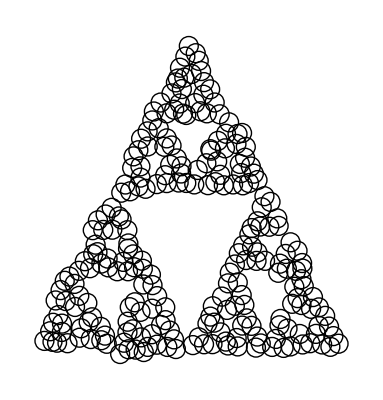

```mathematica
rr := RandomReal[{-0.01, +0.01}];
split[{{x_, y_}, w_}] := {{{x + rr, y + rr}, w/2}, {{x+w/2 + rr, y + rr}, w/2}, {{x+w/4 + rr, y+w/2 + rr}, w/2}};
coords = { {{0, 0}, 1}};
Do[ coords = Flatten[Map[split, coords], 1], {i, 1, 5}];
Graphics[Map[Apply[Circle], coords]]
```

Menger sponge is a closely related fractal shape, filling up a roughly 2.7260-dimensional subspace inside the plain old three-dimensional space. The sponge consists of 27 small cubes arranged as a larger cube, after which the seven cubes in the center and middle of each face are removed. Each cube is then recursively split the same way, in principle infinitely deep, but we can stop once each cube gets small enough for our purposes. (To make the picture more interesting, we will also occasionally randomly stop the splitting, just because.) Note the use of Sow and Reap to build the list of cuboids one element at the time. To make the individual cubes to stand out better, we make them slightly smaller than the volume that they should actually inhabit. Since the Mathematica function Graphics3D produces images that tend to be blocky and not look so good, unlike Graphics that operates on two-dimensional plane and does its own anti-aliasing, image deconvolution with a small kernel is used to make the two-dimensional result image look a bit more natural.

```mathematica
mengercf = ColorData["ArmyColors"];
menger[0, x_, y_, z_, w_] := {mengercf[RandomReal[]],Cuboid[{x + 0.1w, y+0.1w, z+0.1w}, {x+0.9w, y+0.9w, z+0.9w}]};
menger[d_, x_, y_, z_, w_] :=If[d > 1 ||RandomInteger[] == 1,
Flatten[First[Last[Reap[Table[
If[Boole[i == 1] + Boole[j==1] + Boole[k == 1] < 2,
Sow[menger[d - 1,x + i* w / 3, y + j* w/ 3, z + k * w / 3, w / 3]]], {i, 0, 2}, {j, 0, 2}, {k, 0 , 2}]]]]],
menger[0, x, y, z, w]];
ImageDeconvolve[Image[Graphics3D[menger[3, 0, 0, 0, 1], Boxed-> False, Lighting->"Neutral",Background -> White,ImageSize -> 800]],{{-.2,0,0,0,-.2},{0,.5,1,.2,0},{0,0,0,-.5,.2}}]
```

-Graphics-

Fractal shapes can be much more pleasant to the eye, and certainly much more interesting to program than the cliched and silly exercises such as “Write a loop that outputs an n-by-m rectangle of asterisks on the console”, the question that every introduction to programming book had to contain seemingly by law back in the day. Usually followed by asking you to modify the previous program to output a triangle. (Seriously, how many students today even know what the console is? Kids these days, spoiled rotten. Back in my time we programmed in interpreted Basic with line numbers and dammit, we liked it or else!)

The next function fills the unit rectangle with randomly placed disks of different sizes so that no two disks overlap. The list sofar contains the disks that have been generated so far, and the While loop keeps generating disks until there are enough. The radii of the disks decreases according to the harmonic progression, multiplied by the multiplier parameter. (When calling this function, be careful not to make these parameters such that the total area of generated disks would exceed one, since the function would then never terminate its impossible quest the fill the area without overlaps.) Intersection detection for circles is easy: each generated disk is accepted to the list if its Euclidean distance from every previously generated disk is at least equal to the sum of radii of both disks. The function circlefill produces only a list of coordinates that we can then use to render in various shapes. Since Graphics can do its own anti-aliasing, no image processing techniques are needed for the result have smooth edges on the shapes.

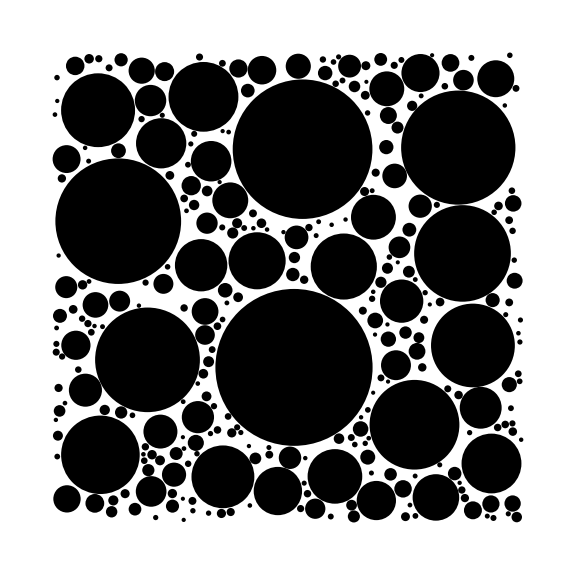

```mathematica
circlefill[n_, start_, mul_] := Module[{sofar,cnt = 1,next, r },
r = 1/(mul * (cnt + start));
sofar = {};
While[cnt < n ,
next = {{RandomReal[{r, 1-r}], RandomReal[{r, 1-r}]}, r};
If[AllTrue[sofar, (EuclideanDistance[next[[1]], #[[1]]] > next[[2]] + #[[2]])&],
PrependTo[sofar, next]; cnt++;r = 1/(mul * (cnt + start))
];
];
sofar
];

Graphics[Map[Apply[Disk, #]&,circlefill[300, 7, 0.75]], ImageSize -> Large]
```

Even though the previous function performs its computations on disks, there is no law of nature or man saying that we must then also render these resulting shapes as disks, as long as we don’t care about the little overlaps that would result. Here is some colourful confetti to cheer you up after sloughing through this material.

```mathematica
Graphics[Riffle[circlefill[300, 7, 0.9], color] /. {{{x_, y_}, r_} :> Rotate[Rectangle[{x-r, y-r}, {x+r, y+r}, RoundingRadius -> 0.02], RandomReal[π]], color :> RGBColor[RandomReal[], RandomReal[], RandomReal[]]}]
```

-Graphics-

Nothing also requires this rendering to be two-dimensional. The next example uses a substitution rule to convert the list into cuboids and colour objects, which are then flattened into a list that Graphics3D can convert to visual form by projecting it onto the two-dimensional viewing plane, of which the actual image forms a finite peephole shown to the human. The argument lists to both Graphics and Graphics3D can consist of both shapes and graphical options, each option used to render the rest of the list until some later option changes it.

```mathematica
ImageDeconvolve[Image[Graphics3D[{Opacity[0.7],Flatten[circlefill[100, 8, 0.8] /. {{x_, y_}, r_} :>  {RGBColor[(x+y)/2, y, x],Cuboid[{x-r,y-r,0},{x+r, y+r, RandomVariate[ExponentialDistribution[10]]}]}, {1}]}, Boxed -> False, Background -> White], ImageSize -> 600],{{0,.5,0},{.2,-1,.8},{.25,0,.25}}]
```

-Graphics-

I also wanted to also use another distribution for the heights but don’t feel like writing that piece of code twice... but hey, this language is more homoiconic than Judy Garland. The piece of code that was used to produce the previous picture is itself a symbolic expression, and therefore we can perform any substitution to it... the only thing to remember is to use Hold to prevent Mathematica from first simplifying that expression before the substitution is performed. Without the Hold, since the result of simplifying the expression would be a Graphics3D expression, it would then be too late to try to substitute a different distribution.

```mathematica
un = Hold[In[$Line - 1]] /. ExponentialDistribution[p_] -> UniformDistribution[{1/10, 1}] // ReleaseHold
```

-Graphics-

The function Rasterize can be used to convert any Graphics object to an image, after which Mathematica’s array of image manipulation functions can be unleashed on it. Since the Graphics objects are symbolic expression, in principle they have an infinite resolution, and can therefore be rasterized to any actual pixel resolution, given either as dots per inch, or an actual pixel dimensions. Once you rasterize some graphic, all symbolic information about the process that generated that graphic is lost, and you can no longer freely rotate and manipulate the graphic, except in the trivial sense of the two-dimensional pixel raster that it has become.

```mathematica
KuwaharaFilter[Rasterize[un,"Image",ImageResolution->72], 5]
```

-Graphics-

The previous example used $Line, one of the many global variables that are used behind the scenes in the Mathematica kernel. By convention, the names of Mathematica global variables always start with the dollar sign to inform the reader that they are global variables, and at the same time, prevent you from accidentally modifying them by defining what you think is a local variable. Historically, the dollar sign was one of the few special characters available in the limited character sets of olde-timey computers, which is why this symbol tends to play some important role unrelated to money in almost every programming language. It is also visually quite distinct from all other characters, which makes it a good separator character for typewriter style console output. To illustrate this, see how long it takes you to visually count the dollar signs in the randomly generated table.

```mathematica
charset = Join[CharacterRange["a", "z"], CharacterRange["0", "9"], {"$"}];
TableForm[Table[RandomChoice[charset], {i, 1, 15}, {j, 1, 15}], TableSpacing -> {1.5, 1.5}]
```

h | c | 2 | w | o | j | i | 3 | 0 | y | 7 | w | e | a | k
$ | $ | 7 | q | u | 6 | 0 | x | a | t | m | i | x | c | d
h | r | c | 0 | 5 | 4 | d | x | c | w | o | r | 0 | b | $
v | 7 | j | j | q | q | p | 5 | z | v | z | 5 | 2 | l | 6
n | y | 2 | z | e | 7 | p | 3 | x | n | k | 6 | q | f | d
8 | y | s | z | 1 | f | 5 | k | $ | x | x | h | y | b | j
s | f | m | i | n | y | m | c | n | 5 | t | 8 | 4 | s | q
n | i | o | 5 | 5 | r | a | b | c | o | z | 9 | u | 1 | a
y | $ | v | z | m | 0 | n | 5 | 1 | 3 | 7 | k | 6 | i | m
e | a | c | d | q | 7 | k | u | u | 7 | s | t | k | 8 | s
2 | 3 | w | b | u | z | 3 | m | a | 3 | h | c | $ | n | 2
k | y | $ | 8 | r | z | q | n | 7 | 6 | z | q | 0 | 5 | u
4 | e | c | 4 | 4 | 7 | e | h | 1 | q | g | l | t | x | f
9 | h | t | o | y | q | 3 | y | t | k | r | 0 | o | g | e
6 | d | 2 | 1 | i | 9 | n | n | h | v | g | m | 6 | q | p

Finally, a trippy variation where the balls are also allowed to nest inside each other, as long as their edges don’t cross but at most kiss. The result is a bit reminiscent of the aesthetics of the seventies.

```mathematica
circlefill2[n_, start_, dup_] := Module[{sofar,cnt = 1,next, r },
r = 1/(Floor[cnt/ dup] + start);
sofar = {};
While[cnt < n ,
next = {{RandomReal[{r, 1-r}], RandomReal[{r, 1-r}]}, r};
If[AllTrue[sofar, (EuclideanDistance[next[[1]], #[[1]]] > next[[2]] + #[[2]] || EuclideanDistance[next[[1]], #[[1]]] +r < #[[2]])&  ],
PrependTo[sofar, next]; cnt++;r = 1/(Floor[cnt/dup] + start)
];
];
sofar
];

ImageDeconvolve[ImageEffect[Image[Graphics[{Thick,Map[Apply[Circle, #]&,circlefill2[500, 7, 4]]}, Background -> White,ImageSize -> 600]],{"PoissonNoise", .1}],{{-.5,0,-.5},{1,1,1},{-.5,0.,-.5}}]
```

-Graphics-

Alternatively, we can use pattern matching and substitution to convert the circle coordinates to cylinder coordinates, and then apply Cylinder to create a three-dimensional shape. This works fine here since a circle inside a larger circle will necessarily have a smaller radius, so when we define the heights to be inversely related to radius, it all works out smoothly.

```mathematica
ImageConvolve[Image[With[{cf = ColorData["SouthwestColors"]},Graphics3D[Map[{cf[RandomReal[]],Apply[Cylinder,#]}&,(circlefill2[75, 7, 4] /. {{x_, y_}, r_} -> {{{x, y, 0}, {x, y, 1/(1+30 r)}}, r})], Boxed-> False]], ImageSize -> 600],DiamondMatrix[2]/ Total[DiamondMatrix[2],2]]
```

-Graphics-

The previous algorithm could be adapted to fill not just the unit square, but any region inside of which we can generate a random point. The easiest way to do this might be to roughly precompute the distances for each point in pixel resolution with image processing. For our next example, we shall consult the CountryData knowledge base to create a geometrical shape of “Francegon”, which we first convert to an image that is next binarized to use white foreground and black background, and finally distance transformed so that the brightness of each pixel denotes its distance from the nearest background pixel.

```mathematica
francegon = Polygon[First[First[CountryData["France", "Polygon"]]]];
franceimg = ImageReflect[ImageRotate[ColorNegate[Image[Graphics[francegon, AspectRatio -> Automatic]]]], Left->Right];
francedist = ImageAdjust[DistanceTransform[franceimg]]
```

-Graphics-

Next, a variation of random filling that uses image pixel value, adjusted to range [0, 1], as the approximate distance metric from the border. We use the binomial distribution to generate random integer radii so that the distribution of these shapes is more pleasant to look at. In the loop that generates the circles one at the time, we maintain the current parameter of this distribution adaptively in the local variable cp that is decremented at every failure to generate a fitting circle, and incremented at every success. This way, the distribution gets tighter as the shape fills up with circles and it becomes ever more difficult to find the next free space. No force can stop you from trying out other distributions, both discrete and continuous, in place of the binomial distribution to observe their effect to the final result. However, distributions that allow very large circles tend to end up aesthetically unpleasant, the result consisting of a couple of big circles accompanied by lots of pixel-sized dots.

```mathematica
imgfill[n_, dmax_, dmin_, dimg_] := Module[{iw, ih, x, y, sofar,cnt = 1,next, r, cp},
sofar = {};
iw = ImageDimensions[dimg][[1]];
ih = ImageDimensions[dimg][[2]];
cp = dmax;
While[cnt < n ,
x = RandomInteger[{1, iw}];
y = RandomInteger[{1, ih}];
cp = Min[dmax, cp];
r = RandomVariate[BinomialDistribution[cp, 3/4]] + 2;
r = Min[{r, Min[{iw, ih}]*PixelValue[dimg,{x, y}]}];
If[ r > 2 &&AllTrue[sofar, (EuclideanDistance[{x,y}, #[[1]]] > r + #[[2]])&  ],
PrependTo[sofar, {{x, y}, r}]; cnt++; cp = cp + 5,
If[cp > dmin, cp--]
];
];
sofar
];
```

Now we can fill France with, say, random pentagons. As long as we have keep each rendered shape inside the circle that it is computed from, those shapes can’t intersect each other, since their bounding circles don’t. Note that the island of Corsica is considered to be part of France, so that the Francegon is actually split into multiple pieces. Since the function Polygon can handle a list of lists of points to represent such polygon soup (should we perhaps call this particular one bouillabaisse?), this poses no problem.

```mathematica
ngon[n_, r_] := Polygon[Table[{r Cos[2π i/n], r Sin[2 π i / n]}, {i, 1, n+1}]];
Graphics[Riffle[imgfill[400, 20, 2,francedist], color] /. {{{x_, y_}, r_} :> Translate[Rotate[ngon[5,r], RandomReal[{-π/10, π/10}]], {x, y}], color:> RandomChoice[{Red, Blue}]}, AspectRatio->Automatic]
```

-Graphics-

Let us return to integers for a moment. For the given positive integer n, how many numbers between n and 2n, inclusive, are prime numbers?

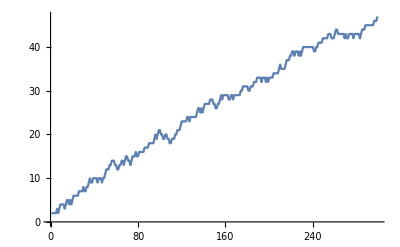

```mathematica
countprimes[n_] := Module[{count = 0, i},
Do[ count = count + Boole[PrimeQ[i]],{i, n, 2n}];
count
]
ListLinePlot[Table[countprimes[i], {i, 2, 300}]]
```

Note how any condition written with If whose result is either 1 or 0 can always be written in a simpler fashion by applying to its condition the handy conversion function Boole that maps truth values to integers. In mathematical functions, you can for example use this function to integrate some function over some region by defining that function to be zero outside your region.

```mathematica
Integrate[Boole[x^2 + y^3 ≤ 1] * (4x^- 7x y + y^2), {x, -2, 2}, {y, -2, 2}]
```

1/9720(13068+(640 (3 ⅈ+√3) π^(3/2))/(Gamma[1/6] Gamma[4/3])-3^(2/3) (3171+2240 Hypergeometric2F1[-5/6,1,1/2,4]+13920 Hypergeometric2F1[1/6,1,1/2,4]))+∫_-1^1 (3-8/x^6-x^2/3+(2 (1-x^2)^(2/3))/x^6)ⅆx

Here is another problem to solve with loops: does the given list contain any two elements that together add up to zero? To answer this question, we need to loop through all possible pairs of element locations. The function Do can do this for any number of loop counter variables, so that there is no need to nest these loops inside one other. (Of course you could do that, but it would be more difficult to follow.) Inside a loop, as soon as you know that your job is done so that the answer can no longer change no matter how much more computations you do, the function Break can be used to terminate the current loop prematurely. This is typical in problems involving finding one example or one counterexample: once you find what you are looking for, it doesn't matter how many more such examples exist.

```mathematica
containsopposites[list_] := Module[{i, j, answer, len},
answer = False;
len = Length[list];
Do[
If[list[[i]] + list[[j]] == 0, answer = True; Break[]];,
{i, 1,len}, {j, i+1, len}
];
answer
];
containsopposites[{2, 3, -4, jimmy, 7}]
```

False

```mathematica
containsopposites[{2, hello, 1, -hello, 4}]
```

True

Note the order in which the loop counter variables i and j are defined in the end of the Do-loop. The iteration goes through the range of values of the first variable i, and for each such value, goes through all values of in the range of j. If this range depends on the current value of i, as it does in the above example, it is essential that the loop counter variables are defined in this order. If you switched the order of the loop counter variable range definitions, the containsopposites function would no longer work correctly.

Loops are also a pretty convenient way to generate the integer spiral matrix. Any reader who can compute that one using pure functional programming obviously knows what they are doing.

```mathematica
outofbounds[i_, j_, n_] := i < 1 || j < 1 || i > n || j > n;
dirs = {{0, 1}, {1, 0}, {0, -1}, {-1, 0}};
spiral[n_] := Module[{i, j, matrix, count, dir, ni, nj}, 
matrix = ConstantArray[0, {n, n}];
i = 1; j = 1; count = n*n; dir = 1;
While[count > 0,
matrix[[i]][[ j]] = count;
count--;
ni = i + dirs[[dir]][[1]];
nj = j + dirs[[dir]][[2]];
If[outofbounds[ni, nj, n] || matrix[[ni]][[ nj]] > 0,
dir = dir + 1;
If[dir == 5, dir = 1];
ni = i + dirs[[dir]][[1]];
nj = j + dirs[[dir]][[2]];
]
i = ni; j = nj;
];
matrix
]

spiral[6] // MatrixForm
```

(36 | 35 | 34 | 33 | 32 | 31
17 | 16 | 15 | 14 | 13 | 30
18 | 5 | 4 | 3 | 12 | 29
19 | 6 | 1 | 2 | 11 | 28
20 | 7 | 8 | 9 | 10 | 27
21 | 22 | 23 | 24 | 25 | 26)

Rendering an integer spiral with only the prime number elements plotted produces the famous Ulam spiral. If you generate this diagram big enough and squint hard enough, you might even imagine seeing all sorts of wonderful patterns in how the prime numbers are distributed within all integers.

```mathematica
MatrixPlot[Map[Boole[PrimeQ[#]]&, spiral[50]], ColorFunction -> "Monochrome"]
```

-Graphics-

That one works straightforwardly with only one level of Map since PrimeQ and Boole are both Listable and can therefore be applied to each entire row of elements at once. If your function is not Listable, just give the correct level specification as the third argument to Map.

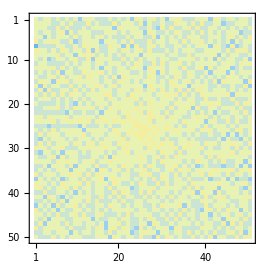

```mathematica
MatrixPlot[Map[Length[FactorInteger[#]]&, spiral[50], {2}], ColorFunction -> "Pastel"]
```

## Rendering fractals with loops

An iterated function system (IFS) is a way to generate complex and beautiful fractal shapes not by subdivision but by plotting the course of some function towards its strange attractor. Starting from some initial point on the plane, repeatedly calculate the next point by applying some function to your current point, keeping track in a matrix of the count of how many times the iteration has visited each pixel. After enough iterations, you render each pixel according to its visit count, using some suitable colour scheme that scales the counts between zero and the maximum count of any pixel. This sequence of points does not visit all pixels equally often, but spends most of its time in the attractors of the function being iterated.

The following example that renders the pretty DeJong attractor is adapted and simplified from a reply in the Stack Exchange Mathematica subforum by the user “gleno”.  Note that the list called matrix is one-dimensional while the algorithm iterates through the sequence, and gets partitioned into a two-dimensional list of lists only after the iteration of the point sequence has terminated.

```mathematica
dejong[dim_, params_, iters_]:=Module[{matrix,d1,d2,a,b,c,d,x,y,iter,xp,xn,yp,yn, max},matrix=Table[0.0,{dim dim}];
{a,b,c,d}=params;
{x,y,iter} = {0, 0, 0};
{d1,d2}={1+0.5 (dim-1),0.25 (dim-1)};
While[++iter<iters,
xn=Sin[a y]-Cos[b x];
y=Sin[c x]-Cos[d y];
x=xn;
xp=Floor[d1+d2 x];
yp=Floor[d1-d2 y];
++matrix[[yp dim+xp]];
];
max=Max[matrix];
matrix = Map[(Sqrt[#]/max)&, matrix];
matrix = Partition[matrix, dim];
Colorize[ArrayPlot[matrix,ImageSize->dim,Frame->False], ColorFunction->"SunsetColors"]
];

dejong[500,{1.4,-2.3,2.4,-2.1},3000000]
```

-Graphics-

Substitution rules lend themselves naturally to L-Systems. They can be used to give instructions to turtle graphics where a turtle can either move forward to its current direction, or turn left or right as seen from its own point of view. The function kochcurve implements the classic Koch curve with given number of levels and step size.

```mathematica
kochcurve[lvl_, sx_, sy_, sϕ_] := Module[{moves,x, y, ϕ, m, i, lines},
moves = {fwd};
Do[moves = Flatten[moves /. fwd -> {fwd, left,fwd, right, fwd, right, fwd, left, fwd}],
{i, 1, lvl}
];
x = sx; y = sy; ϕ = sϕ;
{dummy, {points}} = Reap[
Do[
m = moves[[i]];
If[m == fwd, Sow[{x,y}]; {x,y} = {x + Cos[ϕ], y + Sin[ϕ]}];
If[m == left, ϕ = ϕ + π / 3];
If[m == right, ϕ = ϕ - π / 3];
, {i, 1, Length[moves]}
]
];
points
];
```

The previous function returns the list of points on the Koch curve. It is up to the user of this function to decide how those points get rendered and what kind of geometric shapes are used to render them. The function Text can be used to draw text as a graphical primitive. Just to have a bit of fun, the next example showcases various functions that can be used to decorate other symbols.

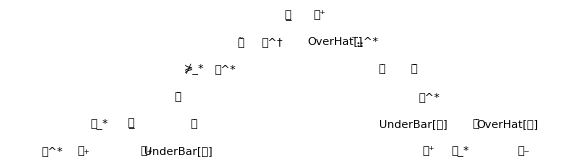

```mathematica
fx := RandomChoice[{SubPlus, SubMinus, SubStar, SuperPlus, SuperMinus, SuperStar, SuperDagger, OverBar, OverVector, OverTilde, OverHat, OverDot, UnderBar}];
Graphics[kochcurve[2, 0, 0, 0] /. {x_, y_} :> Style[Text[fx[FromCharacterCode[RandomInteger[{1000,20000}]]], {x,y}], FontSize ->20], ImageSize-> Large]
```

Here is a mirrored Koch curve with each segment drawn as a randomly pointed line.

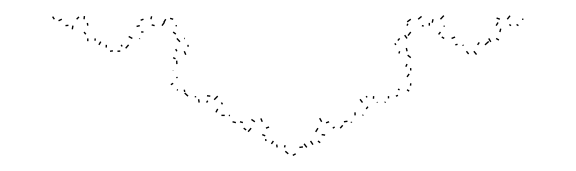

```mathematica
Graphics[kochcurve[3, 0, 0, 0] /. {x_, y_} :> Line[{{x, -y}, {x+RandomReal[{-.5,+.5}], -y + RandomReal[{-.5, +.5}]}}], ImageSize-> Large]
```

A table of multiple Koch curves rendered with randomly oriented triangles.

```mathematica
triangle[x_, y_] := Scale[Rotate[Triangle[{{x-1/2, y-1/4}, {x+1/2,y-1/4}, {x, y+1/2}}], rot], sca] /. {rot :> RandomReal[{0, π}], sca:> RandomReal[{0.5, 1.5}]};

Graphics[Table[kochcurve[2, 0, 0, k*2π/( 10)] /. {x_, y_} :> triangle[x, y], {k, 0, 9}], ImageSize -> Large]
```

-Graphics-

The next fractal will illustrate several techniques in one swoop. In a diffusion system, the fractal consists initially of a set of points, in this example for simplicity only one point positioned at the origin. One at the time, new points are created randomly in the surrounding space, and these points move around in some random walk fashion until they come close enough to some existing point already in the fractal. When this happens, the existing point becomes the parent of the new point, and the new point is added to the set, stationary at the location where it ended up. In the following example, to ensure that the random walk will find another point soon enough instead of heading off toward infinity as these random walks are prone to do, we make each point “fall” towards the origin, and move randomly only “sideways” by adding a normally distributed random quantity to its angle from the origin.

```mathematica
closestidx[p_, particles_] := First[Ordering[Map[EuclideanDistance[p, #]&, particles], 1]];

diffuse[d_, thres_, n_] := Module[{dcurr, ϕcurr, particles, parents, r, ϕ, p},
particles = {{0, 0}};
parents = {1};
dcurr = d;ϕcurr = 0;
Do[
r = dcurr;
ϕcurr = ϕ = ϕcurr + RandomReal[{π/4, π/ 2}];
p ={r Cos[ϕ], r Sin[ϕ]}; 
While[EuclideanDistance[p, particles[[closestidx[p, particles]]]] > thres,
r = r * 0.97;
ϕ = ϕ + RandomVariate[NormalDistribution[0, π / 10]];
p ={r Cos[ϕ], r Sin[ϕ]};
];
AppendTo[parents, closestidx[p, particles]];
AppendTo[particles, p];
If[r > 0.95 * dcurr, dcurr = dcurr * 1.01];
, {i, 1, n}];
{particles, parents}
];
```

The above function diffuse returns two lists, the first list containing the points as plain lists of two coordinates, and the second list containing the index of the parent of each point. We can then render these points connected to their parents as line segments, to create a pattern that resembles a crack in glass or similar material.

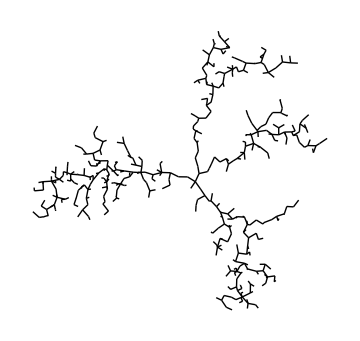

```mathematica
diffuselines[{particles_, parents_}] :=
MapIndexed[Line[{#1, First[particles[[parents[[#2]]]]]}]&, particles];
Graphics[diffuselines[diffuse[1, 0.05, 500]], ImageSize-> Medium]
```

A much more organic and natural looking image can be generated by connecting each point not to just its immediate parent using one straight line segment, but by creating a spline curve from each point to its parent, grandparent, great grandparent, and so on. The thickness parameter len in the function diffusesplines determines how many points down the parentage line each spline curve passes through.

```mathematica
diffusesplines[{particles_, parents_}, len_] :=  
First[Map[BSplineCurve[#]&, 
Map[particles[[#]]&,
Flatten[MapIndexed[NestList[parents[[#]]&, #2, len]&, parents], {3}], {2}
], {2}
]
];
Graphics[diffusesplines[diffuse[1, 0.05, 500], 5], ImageSize-> Medium]
```

-Graphics-

Again, no law of nature or man says that we could not extend the space to the third dimension, except that when the tyrant is the anonymous law, modern man believes he is free. In this particular case, we still can’t make the screen to be three-dimensional, so we shall do all that we can do, benevolently pretend in consensus that the two-dimensional pixel raster somehow contains three dimensions. This would be akin to believing that a picture of a crocodile could eat you. Image deconvolution is again used to smooth out the jagginess of Graphics3D, but this time with a random kernel. In both image convolution and deconvolution, the kernel entries should add up to one so that the operation maintains the overall brightness of the image.

```mathematica
diffusecylinders[{particles_, parents_}] := Module[{parts},
parts = ReplaceAll[particles, {x_, y_} :> {x, y, RandomReal[{-0.03, 0.03}]}];
MapIndexed[Cylinder[{#1, First[parts[[parents[[#2]]]]]}, 0.05]&, parts]
];
With[{m = RandomReal[{-.5,.5},{3,3}]},
With[{kernel = m / Total[m,2]},ImageDeconvolve[Image[Graphics3D[diffusecylinders[diffuse[1, 0.05, 500]], Boxed-> False,Background -> White, ViewAngle -> 18 Degree,ImageSize -> 600]],kernel]]]
```

-Graphics-

The ability to freely mix functional, rule-based and imperative programming makes many things surprisingly straightforward in Mathematica. However, no matter how much the syntax of Mathematica resembles mathematics, the programs written in that language still do not get executed inside some abstract Platonic realm of pure mathematical ideas that somehow magically exists outside time and space. Everything that the computer does ultimately happens by the processor executing machine code instructions to read and modify the values of bytes in the memory. This is not affected by how many layers of more or less leaky abstractions we pile on top of that physical reality to make things easier for us humans who need to be very humble with the low capacity of our small brains to keep track of several levels of things happening at once.

The more these abstractions hide the underlying reality, the easier it becomes to accidentally write a function that is correct in principle, but whose execution becomes very slow as its argument values get larger. To illustrate this, let us write in contrasting styles the exact same mathematical function that produces a list of random integers where each element produced from the previous one by adding a random positive quantity to it, and then measure and plot their execution time.

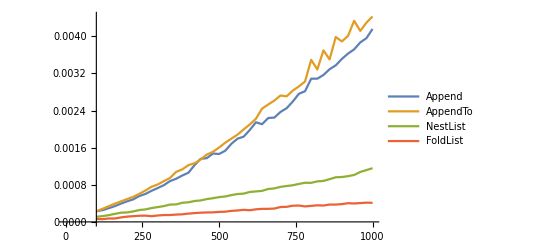

```mathematica
rand := RandomInteger[{1, 10}];

ri1[n_] := Module[{i, result, total},
total = rand;
result = {total};
Do[total = total + rand; result = Append[result, total], {n-1}];
result
];

ri2[n_] := Module[{i, result, total},
total = rand;
result = {total};
Do[total = total + rand; AppendTo[result, total], {n-1}];
result
];

ri3[n_] := NestList[(# + rand)&, rand, n-1];

ri4[n_] := FoldList[Plus, rand, Table[rand, {n-1}]]

sample[f_, n_, samples_] := First[Timing[Do[f[n], {samples}]]] / samples;

ri1data = Table[{i, sample[ri1, i, 100]}, {i, 100, 1000, 20}];
ri2data = Table[{i, sample[ri2, i, 100]}, {i, 100, 1000, 20}];
ri3data = Table[{i, sample[ri3, i, 100]}, {i, 100, 1000, 20}];
ri4data = Table[{i, sample[ri4, i, 100]}, {i, 100, 1000, 20}];
ListLinePlot[{ri1data, ri2data, ri3data, ri4data}, AxesOrigin->{100, 0},PlotLegends->{"Append", "AppendTo", "NestList", "FoldList"}]
```

A very dramatic difference that only grows larger over time! The running time of NestList and FoldList implementations is linear with respect to the problem size: producing twice as many numbers should take roughly twice as long. However, the imperative programming solutions have a quadratic running time so that producing twice as many numbers will take roughly four times as long, producing three times as many numbers will take roughly nine times as long, and so on.

The explanation for this is that the functions Append and AppendTo always have to produce a new list when they append one element. This necessitates the copying of all of the previous elements of the list. When the list gets longer, the same elements get copied and copied over and over each time a new element is added. Algorithms that behave this way are known as Poor Shlemiel algorithms, as in the old joke about Shlemiel tasked to paint a long fence. His job keeps getting slower and more tedious, because the further down the fence Shlemiel advances, the longer it takes for him to run back to the beginning to dip his brush into the bucket of paint that he keeps firmly stationed there. As silly as this sounds, many algorithms do essentially this very thing, under the substitution fence /. list. You can surely find many examples of this in the documents written by this author.

(The little fluttering of these running time sampling curves is caused by another leaky abstraction. Because the Mathematica computation kernel has to do occasional internal housekeeping between and in the middle of doing the things that you actually asked it to do, and it has to compete for the CPU time with all the other processes that are running inside your computer at the same time, it can’t possibly serve your needs in the same constant speed at all times.)

A linear-time imperative solution is possible by first generating the entire list at once, and then modifying its elements in place without copying the entire list each time.

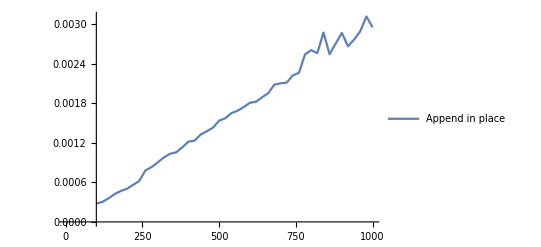

```mathematica
ri5[n_] := Module[{result},
result = Table[0, {n}];
result[[1]] = rand;
Do[result[[i]] = result[[i-1]] + rand, {i, 2, n}];
result;
];

ListLinePlot[Table[{i, sample[ri5, i, 100]}, {i, 100, 1000, 20}], AxesOrigin->{100, 0},PlotLegends->{"Append in place"}]
```

Speaking of long running times, we conclude this lesson with a longer example of rendering the Buddhabrot, an alternative way to visualize the famous Mandelbrot fractal set. Instead of iterating the equation from the given starting pixel and colouring it black if the iteration doesn’t escape, the Buddhabrot algorithm works in a sense reverse to that in that it maintains a counter for each pixel, initially zero. The algorithm then repeatedly chooses a random point from the complex plane and iterates it along the Mandelbrot equation some fixed number of steps, or until that point escapes. If this iteration does not escape within that step limit, every pixel that that iteration visited gets its counter incremented by one.

As more sequences from random starting points have been iterated, a shape that vaguely resembles a meditating Buddha will gradually emerge. To make this shape easier to see, the Buddhabrot fractal is usually rendered with its real and imaginary axis rotated 90 degrees from the typical Mandelbrot renderings so that the shape ends up in the sitting position. As is also common in Buddhabrot renderings, the red, green and blue components of the resulting image are computed with a different “exposure” to better bring out the detail of the Buddhabrot. Since the Buddhabrot, just like the Mandelbrot set, is symmetric assuming that the formula uses an exponent that is an even integer, we can increment two symmetric pixels each time and save half of the work and produce a perfectly symmetric image that is more pleasant for us ogle at and meditate the deep truths of the multiverse. In the ordinary Mandelbrot set, the set itself is all black, as is appropriate for a concept that is equivalent to a black hole that the sequence can never escape from, and we care about the shape of its boundary and the escape times of its outside points, but the Buddhabrot reveals the internal structure of this black hole.

The famous expression says that you can always write Fortran in any language, and so the following implementation evokes the vague unease about how Edgser W. Dijkstra would not have liked this. The reader is invited to elevate the following code towards a less imperative spirit.

```mathematica
buddhabrot[px_, py_, maxiter_, n_] := Module[{red, green, blue, series, i, z0, z, x, y1, y2, rmax, gmax, bmax, pixels},
red = Table[0, {i, 1, px}, {j, 1, py}];
green = Table[0, {i, 1, px}, {j, 1, py}];
blue = Table[0, {i, 1, px}, {j, 1, py}];
pixels = Table[0, {i, 1, px}, {j, 1, py}];
Do [
i = 1;
z =z0 = RandomReal[{-1.5, 1.5}] + I RandomReal[{-1.5, 1.5}];
series = {z};
While[i ≤ maxiter && Abs[z] < 1.5,
i++;
z = z ^2 + z0;
AppendTo[series, z];
];
If[Abs[z] < 1.5,
Do[
x = Ceiling[(Re[series[[i]]]+1.5)/3*px];
y1 = Ceiling[(Im[series[[i]]]+1.5)/3*py];
y2 = py + 1 - y1;
If[i < maxiter / 10, red[[x]][[y1]]++; red[[x]][[y2]]++];
If[i < maxiter / 3, green[[x]][[y1]]++; green[[x]][[y2]]++;];
blue[[x]][[y1]]++;
blue[[x]][[y2]]++,
{i, 1, Length[series]}
];
]
, {n}
];
rmax = Max[red];
red = Power[red/ rmax, 1/4];
bmax = Max[blue];
blue = Power[blue / bmax, 1/4];
gmax = Max[green];
green = Power[green / gmax, 1/4];
Do[pixels[[x]][[y]] = {red[[x]][[y]],green[[x]][[y]], blue[[x]][[y]] }, {x, 1, px}, {y, 1, py}];
Image[pixels,ImageSize -> Large]
];

buddhabrot[500, 500, 30, 500000]
```

-Graphics-

Good Buddhabrot renderings tend to take quite a while, and can therefore always use heavy performance tune-ups with both algorithmic optimizations and micro-optimizations. If executed for some decent image size so that the system is iterated perhaps a hundred million rounds instead of just some couple hundred thousand, the rendering task is surely best left brewing overnight while we enjoy the Sandman’s dream cabaret.